## 0. Functions

### FindRoot - Broyden’s Method - TryBroydenFindRoot[function, initialGuess, accuracy, maxIterations]

<summary>
Helper method to calculate an approximation of the Jacobian.
< /summary >
< param name = "f" > The function. < /param >
< param name = "x0" > The argument (initial guess). < /param >
< param name = "y0" > The result (of initial guess). < /param >

#### Calculate Approximate Jacobian

```mathematica
CalculateApproximateJacobian[f_,x0_,y0_]:=Module[
{dim,B,x,h,xj,y,i,j},
dim =Length[x0];
B=ConstantArray[0,{dim,dim}];
x=x0;

For[j=1,j≤ dim,j++,
h=Abs[x0[[j]]];
If[h==0,h=0.0001];

xj=x[[j]];
x[[j]]=xj+h;
y=f[x];
x[[j]]=xj;

For[i=1,i≤ dim,i++,
B[[i,j]]=(y[[i]]-y0[[i]])/h;
];
];
Return[B];
];
```

< summary > Find a solution of the equation f (x) = 0. < /summary >
< param name = "f" > The function to find roots from. < /param >
< param name = "initialGuess" > Initial guess of the root. < /param >
< param name = "accuracy" > Desired accuracy.The root will be refined until the accuracy or the maximum number of iterations is reached. < /param >
< param name = "maxIterations" > Maximum number of iterations.Usually 100. < /param >
< param name = "root" > The root that was found, if any.Undefined if the function returns false. < /param >
< returns > True if a root with the specified accuracy was found, else false. < /returns >

#### FindRoot

```mathematica
TryBroydenFindRoot[f_,initialGuess_, accuracy_, maxIterations_]:=Module[
{
x,y0,y,g,dx,xnew,ynew,gnew,B,g2,scale,root,dF,dB
},
x=initialGuess;

y0=f[initialGuess];
y=y0;
g=Norm[y];

B=CalculateApproximateJacobian[f,initialGuess,y0];

For[i=1,i≤ maxIterations,i++,
dx=-Inverse[B].y;
xnew=x+dx;
ynew=f[xnew];
gnew=Norm[ynew];

If[gnew>g,
g2=g*g;
scale=g2/(g2+gnew*gnew);
If[scale==0,scale=0.0001];

dx=scale*dx;
xnew=x+dx;
ynew=f[xnew];
gnew=Norm[ynew];
];

If[gnew<accuracy,
Return[{"Solution"->xnew,"Success"->True}];
];

dF=ynew-y;
dB=(dF-B.dx).(dx*1/(Norm[dx]^2));
B=B+dB;

x=xnew;
y=ynew;
g=gnew;
];
Print["Not Converge! Residue : "<>ToString[gnew]];
Return[{"Solution"->xnew,"Success"->False}];
];
```

#### Demo

```mathematica
(*F1[u_]:={u,1/5*u*u-10};
F2[v_]:={9,3}+v*{2,3};
EquaSet[x_]:=Module[
{x1,y1,x2,y2},
{x1,y1}=F1[x[[1]]];
{x2,y2}=F2[x[[2]]];
Return[{x1-x2,y1-y2}];
];*)
```

```mathematica
(*Ans="Solution"/.TryBroydenFindRoot[EquaSet,{0,0},0.00000001,100]*)
```

```mathematica
(*EquaSet[Ans]
Diagram1=ParametricPlot[{F1[u],F2[v]},{u,-10,10},{v,-10,10}];
AnsPlot=Graphics[{
Blue,PointSize-> 0.03,Point[F1[0]],
Blue,PointSize-> 0.03,Point[F2[0]],
Red,PointSize-> 0.03,Point[F1[Ans[[1]]]]
}];
Show[{Diagram1, AnsPlot}]*)
```

### 對任意軸旋轉的座標轉換矩陣

```mathematica
GetRotateMatrix3[direction_,angle_]:=Module[{
angleZ,angleY,
A21,A32,ARotate,A23, A12
},
angleZ=If[direction[[1]]≠0||direction[[2]]≠0,
ArcTan[direction[[1]],direction[[2]]],
0];
angleY=-ArcTan[Norm[Take[direction,2]],direction[[3]]];
A21=({{Cos[-angleZ], -Sin[-angleZ], 0}, {Sin[-angleZ], Cos[-angleZ], 0}, {0, 0, 1}});
A32=({{Cos[-angleY], 0, Sin[-angleY]}, {0, 1, 0}, {-Sin[-angleY], 0, Cos[-angleY]}});
ARotate=({{1, 0, 0}, {0, Cos[angle], -Sin[angle]}, {0, Sin[angle], Cos[angle]}});
A23=({{Cos[angleY], 0, Sin[angleY]}, {0, 1, 0}, {-Sin[angleY], 0, Cos[angleY]}});
A12=({{Cos[angleZ], -Sin[angleZ], 0}, {Sin[angleZ], Cos[angleZ], 0}, {0, 0, 1}});
Return[A12.A23.ARotate.A32.A21];
];
```

### Non-Uniform B-Spline(NUB)

#### Clamped End Condition - “CreateClampedEndNUBCurve[dataPoints, startWithTangent, endWithTangent]”

```mathematica
CreateClampedEndNUBCurve[dataPoints_,startWithTangent_,endWithTangent_]:=Module[
{
controlPoints,Ni,deltai,lastSegmentIndex,
n,M,invM,R,
i,id,iM,
a0,b0,c0,r0,
an,bn,cn,rn,
t1,t2,
Nci,
Blending,dUBlending,dU2Blending,ParamMapping,
P,dU,dU2,
Output
},
n=Length[dataPoints];
lastSegmentIndex=n-1;
M=ConstantArray[0,{n+2,n+2}];
R=ConstantArray[1,{n+2,3}];

(*計算弦長*)
deltai=ConstantArray[0,n+3];
deltai[[1]]=0;
deltai[[2]]=0;
deltai[[n+2]]=0;
deltai[[n+3]]=0;
For[i=1,i<n,i++,
deltai[[i+2]]=Norm[dataPoints[[i+1]]-dataPoints[[i]]];
];

(*計算M矩陣*)
M[[1,1]]=-3;
M[[1,2]]=3;
M[[2,1]]=1;
M[[n+1,n+2]]=1;
M[[n+2,n+1]]=-3;
M[[n+2,n+2]]=3;
For[i=2,i<n,i++,
id=i+2;
iM=i+1;
(*fi*)
M[[iM,i]]=(deltai[[id]])^2/(deltai[[id-1]]+deltai[[id]])/(deltai[[id-2]]+deltai[[id-1]]+deltai[[id]]);
(*gi*)
M[[iM,i+2]]=(deltai[[id-1]])^2/(deltai[[id-1]]+deltai[[id]]+deltai[[id+1]])/(deltai[[id-1]]+deltai[[id]]);
(*hi*)
M[[iM,i+1]]=1-M[[iM,i]]-M[[iM,i+2]];
];

(*計算R矩陣*);
t1=startWithTangent;
t2=endWithTangent;
If[startWithTangent==Null&&n>2,
a0=dataPoints[[2]]-dataPoints[[1]];
b0=dataPoints[[3]]-dataPoints[[1]];
c0=Cross[a0,b0];
If[Norm[c0]==0,
t1=a0;,
r0=(Norm[a0]*Norm[a0]*Cross[b0,c0]+Norm[b0]*Norm[b0]*Cross[c0,a0])/(2*Norm[c0]*Norm[c0]);
t1=Norm[a0]*Normalize[Cross[r0,c0]];
]
,
If[startWithTangent==Null,
t1=dataPoints[[2]]-dataPoints[[1]];
];
];
If[endWithTangent==Null&&n>2,
an=dataPoints[[n-1]]-dataPoints[[n]];
bn=dataPoints[[n-2]]-dataPoints[[n]];
cn=Cross[an,bn];
If[Norm[cn]==0,
t2=-an;,
rn=(Norm[an]*Norm[an]*Cross[bn,cn]+Norm[bn]*Norm[bn]*Cross[cn,an])/(2*Norm[cn]*Norm[cn]);
t2=-Norm[an]*Normalize[Cross[rn,cn]];
]
,
If[endWithTangent==Null,
t2=dataPoints[[n]]-dataPoints[[n-1]];
];
];

R[[1]]=t1;
R[[n+2]]=t2;
For[i=1,i<n+1,i++,
iM=i+1;
R[[iM]]=dataPoints[[i]];
];

(*計算每個線段的N矩陣*)
Ni=ConstantArray[0,{n-1}];
For[i=1,i<n,i++,
id=i+2;
Nci=IdentityMatrix[4];
Nci[[1,1]]=(deltai[[id]])^2/(deltai[[id-1]]+deltai[[id]])/(deltai[[id-2]]+deltai[[id-1]]+deltai[[id]]);
Nci[[1,3]]=(deltai[[id-1]])^2/(deltai[[id-1]]+deltai[[id]]+deltai[[id+1]])/(deltai[[id-1]]+deltai[[id]]);
Nci[[2,3]]=3*deltai[[id]]*deltai[[id-1]]/(deltai[[id-1]]+deltai[[id]]+deltai[[id+1]])/(deltai[[id-1]]+deltai[[id]]);
Nci[[3,3]]=3*(deltai[[id]])^2/(deltai[[id-1]]+deltai[[id]]+deltai[[id+1]])/(deltai[[id-1]]+deltai[[id]]);
Nci[[4,4]]=(deltai[[id]])^2/(deltai[[id]]+deltai[[id+1]]+deltai[[id+2]])/(deltai[[id]]+deltai[[id+1]]);
Nci[[4,3]]=-1*(1/3*Nci[[3,3]]+Nci[[4,4]]+(deltai[[id]])^2/(deltai[[id]]+deltai[[id+1]])/(deltai[[id-1]]+deltai[[id]]+deltai[[id+1]]));
Nci[[2,1]]=-3*Nci[[1,1]];
Nci[[3,1]]=3*Nci[[1,1]];
Nci[[4,1]]=-Nci[[1,1]];
Nci[[1,2]]=1-Nci[[1,1]]-Nci[[1,3]];
Nci[[2,2]]=3*Nci[[1,1]]-Nci[[2,3]];
Nci[[3,2]]=-(3*Nci[[1,1]]+Nci[[3,3]]);
Nci[[4,2]]=Nci[[1,1]]-Nci[[4,3]]-Nci[[4,4]];
Ni[[i]]=Nci;
];

(*求控制點*)
invM=Inverse[M];
controlPoints=invM.R;

(*曲線方程式*)
(***************************************************************)
Blending[u_,NNci_,cp_]:=Module[
{
tou,blending,p
},
tou={1,u, u^2,u^3};
blending=tou.NNci;
p=blending.cp;
Return[p];
];
(***************************************************************)
dUBlending[u_,NNci_,cp_]:=Module[
{
tou,blending,p
},
tou={0,1, 2*u,3*u^2};
blending=tou.NNci;
p=blending.cp;
Return[p];
];
(***************************************************************)
dU2Blending[u_,NNci_,cp_]:=Module[
{
tou,blending,p
},
tou={0,0, 2,6*u};
blending=tou.NNci;
p=blending.cp;
Return[p];
];
(***************************************************************)
ParamMapping[u_]:=Module[
{
globalU,localU,sIndexU
},
globalU=u*(Length[dataPoints]-1);
localU=Mod[globalU,1];
sIndexU=If[globalU>0,Floor[globalU],Ceiling[globalU]];
sIndexU=sIndexU+1;
If[sIndexU > lastSegmentIndex,
localU=localU+sIndexU-lastSegmentIndex;
sIndexU=lastSegmentIndex;,
If[sIndexU<1,
localU=localU+sIndexU-1;
sIndexU=1;
];
];

Return[{sIndexU,localU}];
];
(***************************************************************)
P[u_]:=Module[
{
mappedParas,sIndexU,localU,cp,NNci,p
},
mappedParas=ParamMapping[u];
sIndexU=mappedParas[[1]];
localU=mappedParas[[2]];
cp=Table[controlPoints[[ii]],{ii,sIndexU,sIndexU+3}];
NNci=Ni[[sIndexU]];
p=Blending[localU,NNci,cp];
Return[p];
];
(***************************************************************)
dU[u_]:=Module[
{
mappedParas,sIndexU,localU,cp,NNci,p
},
mappedParas=ParamMapping[u];
sIndexU=mappedParas[[1]];
localU=mappedParas[[2]];
cp=Table[controlPoints[[ii]],{ii,sIndexU,sIndexU+3}];
NNci=Ni[[sIndexU]];
p=dUBlending[localU,NNci,cp];
Return[p];
];
(***************************************************************)
dU2[u_]:=Module[
{
mappedParas,sIndexU,localU,cp,NNci,p
},
mappedParas=ParamMapping[u];
sIndexU=mappedParas[[1]];
localU=mappedParas[[2]];
cp=Table[controlPoints[[ii]],{ii,sIndexU,sIndexU+3}];
NNci=Ni[[sIndexU]];
p=dU2Blending[localU,NNci,cp];
Return[p];
];
(***************************************************************)
Output={
"DataPoints"-> dataPoints,
"ControlPoints"->controlPoints,
"Ni"->Ni,
"deltai"->deltai,
"LastSegmentIndex"-> lastSegmentIndex,
"Blending"->Blending,
"dUBlending"->dUBlending,
"dU2Blending"->dU2Blending,
"ParamMapping"->ParamMapping,
"P"->P,
"dU"-> dU,
"dU2"->dU2
};

Return[Output];
];
```

#### Circular End Condition - “CreateCirularEndNUBCurve[dataPoints]”

```mathematica
CreateCirularEndNUBCurve[dataPoints_]:=Module[
{
n,
a0,b0,c0,r0,
an,bn,cn,rn,
t1,t2
},
Return[CreateClampedEndNUBCurve[dataPoints,Null,Null]];
];
```

#### Demo

```mathematica
(*DataPoints={
{0,0,0},
{1,-1,0},
{2,3,0},
{3,3,0},
{4,0,0}
};
NUBCurve=CreateCirularEndNUBCurve[DataPoints];
PositionFunc="P"/.NUBCurve;
PositionPlot=ParametricPlot3D[PositionFunc[u],{u,0,1}]*)
```

```mathematica
(*DataPoints={
{0,0,0},
{1,-1,0},
{2,3,0},
{3,3,0},
{4,0,0}
};
NUBCurve=CreateClampedEndNUBCurve[DataPoints,Null,{0,1,1}];
PositionFunc="P"/.NUBCurve;
PositionPlot=ParametricPlot3D[PositionFunc[u],{u,0,1}]*)
```

```mathematica
(*TengantFunc="dU"/.NUBCurve;
TengantPoints=Table[{PositionFunc[u],PositionFunc[u]+TengantFunc[u]},{u,0,1,0.05}];
TengantPlot=Graphics3D[{Green,Line[TengantPoints]}];

CurvatureFunc="dU2"/.NUBCurve;
CurvaturePoints=Table[{PositionFunc[u],PositionFunc[u]+CurvatureFunc[u]},{u,0,1,0.05}];
CurvaturePlot=Graphics3D[{Red,Line[CurvaturePoints]}];

Show[{PositionPlot,TengantPlot ,CurvaturePlot}, PlotRange-> All]*)
```

#### Clamped End Condition - “CreateClampedEndNUBSurface[dataPoints, uTangents, vTangents, InverseNormalDirection]”

```mathematica
CreateClampedEndNUBSurface[dataPoints_,uTangents_,vTangents_, InverseNormalDirection_]:=Module[
{
UCurves,VCurves,
LastSegmentIndexU,
LastSegmentIndexV,
i,
vDataPoints,
ParamMapping,
P,
dU,dU2,
dV,dV2,
dUdV,
N,n,
Output
},
LastSegmentIndexU=Length[dataPoints[[1]]]-1;
LastSegmentIndexV=Length[dataPoints]-1;

UCurves=ConstantArray[0,{Length[dataPoints]}];
For[i=1, i≤ Length[dataPoints],i++,
UCurves[[i]]=CreateClampedEndNUBCurve[dataPoints[[i]],uTangents[[i,1]],uTangents[[i,2]]];
];

VCurves=ConstantArray[0,{Length["ControlPoints"/.UCurves[[1]]]}];
For[i=1, i≤ Length["ControlPoints"/.UCurves[[1]]],i++,
vDataPoints=Table[
("ControlPoints"/.UCurves[[k]])[[i]]
,{k,1,Length[UCurves]}];
If[i==1,
VCurves[[i]]=CreateClampedEndNUBCurve[vDataPoints,vTangents[[1,1]],vTangents[[1,2]]];,
If[i== Length["ControlPoints"/.UCurves[[1]]],VCurves[[i]]=CreateClampedEndNUBCurve[vDataPoints,vTangents[[i-2,1]],vTangents[[i-2,2]]];,
VCurves[[i]]=CreateClampedEndNUBCurve[vDataPoints,vTangents[[i-1,1]],vTangents[[i-1,2]]];
];
];
];


(*曲面方程式*)
(***************************************************************)
ParamMapping[u_,v_]:=Module[
{
uMapping,vMapping
},
uMapping=("ParamMapping"/.UCurves[[1]])[u];
vMapping=("ParamMapping"/.VCurves[[1]])[v];
Return[Join[uMapping,vMapping]];
];
(***************************************************************)
P[u_,v_]:=Module[
{
mappedPara,sIndexU,localU,sIndexV,localV,
uControlPoints,
Nc,
p
},
mappedPara=ParamMapping[u,v];
sIndexU=mappedPara[[1]];
localU=mappedPara[[2]];
sIndexV=mappedPara[[3]];
localV=mappedPara[[4]];

uControlPoints=ConstantArray[0,{4}];
For[i=1,i<=4,i++,
uControlPoints[[i]]=("P"/.VCurves[[sIndexU+i-1]])[v];
];

Nc=("Ni"/.UCurves[[sIndexV]])[[sIndexU]];

p=("Blending"/.UCurves[[1]])[localU,Nc,uControlPoints];
Return[p];
];
(***************************************************************)
dU[u_,v_]:=Module[
{
mappedPara,sIndexU,localU,sIndexV,localV,
uControlPoints,
Nc,
p
},
mappedPara=ParamMapping[u,v];
sIndexU=mappedPara[[1]];
localU=mappedPara[[2]];
sIndexV=mappedPara[[3]];
localV=mappedPara[[4]];

uControlPoints=ConstantArray[0,{4}];
For[i=1,i<=4,i++,
uControlPoints[[i]]=("P"/.VCurves[[sIndexU+i-1]])[v];
];

Nc=("Ni"/.UCurves[[sIndexV]])[[sIndexU]];

p=("dUBlending"/.UCurves[[1]])[localU,Nc,uControlPoints];
Return[p];
];
(***************************************************************)
dU2[u_,v_]:=Module[
{
mappedPara,sIndexU,localU,sIndexV,localV,
uControlPoints,
Nc,
p
},
mappedPara=ParamMapping[u,v];
sIndexU=mappedPara[[1]];
localU=mappedPara[[2]];
sIndexV=mappedPara[[3]];
localV=mappedPara[[4]];

uControlPoints=ConstantArray[0,{4}];
For[i=1,i<=4,i++,
uControlPoints[[i]]=("P"/.VCurves[[sIndexU+i-1]])[v];
];

Nc=("Ni"/.UCurves[[sIndexV]])[[sIndexU]];

p=("dU2Blending"/.UCurves[[1]])[localU,Nc,uControlPoints];
Return[p];
];
(***************************************************************)
dV[u_,v_]:=Module[
{
mappedPara,sIndexU,localU,sIndexV,localV,
uControlPoints,
Nc,
p
},
mappedPara=ParamMapping[u,v];
sIndexU=mappedPara[[1]];
localU=mappedPara[[2]];
sIndexV=mappedPara[[3]];
localV=mappedPara[[4]];

uControlPoints=ConstantArray[0,{4}];
For[i=1,i<=4,i++,
uControlPoints[[i]]=("dU"/.VCurves[[sIndexU+i-1]])[v];
];

Nc=("Ni"/.UCurves[[sIndexV]])[[sIndexU]];

p=("Blending"/.UCurves[[1]])[localU,Nc,uControlPoints];
Return[p];
];
(***************************************************************)
dV2[u_,v_]:=Module[
{
mappedPara,sIndexU,localU,sIndexV,localV,
uControlPoints,
Nc,
p
},
mappedPara=ParamMapping[u,v];
sIndexU=mappedPara[[1]];
localU=mappedPara[[2]];
sIndexV=mappedPara[[3]];
localV=mappedPara[[4]];

uControlPoints=ConstantArray[0,{4}];
For[i=1,i<=4,i++,
uControlPoints[[i]]=("dU2"/.VCurves[[sIndexU+i-1]])[v];
];

Nc=("Ni"/.UCurves[[sIndexV]])[[sIndexU]];

p=("Blending"/.UCurves[[1]])[localU,Nc,uControlPoints];
Return[p];
];
(***************************************************************)
dUdV[u_,v_]:=Module[
{
mappedPara,sIndexU,localU,sIndexV,localV,
uControlPoints,
Nc,
p
},
mappedPara=ParamMapping[u,v];
sIndexU=mappedPara[[1]];
localU=mappedPara[[2]];
sIndexV=mappedPara[[3]];
localV=mappedPara[[4]];

uControlPoints=ConstantArray[0,{4}];
For[i=1,i<=4,i++,
uControlPoints[[i]]=("dU"/.VCurves[[sIndexU+i-1]])[v];
];

Nc=("Ni"/.UCurves[[sIndexV]])[[sIndexU]];

p=("dUBlending"/.UCurves[[1]])[localU,Nc,uControlPoints];
Return[p];
];
(***************************************************************)
N[u_,v_]:=Module[
{
normal
},
If[InverseNormalDirection,
normal=Cross[dU[u,v],dV[u,v]];,
normal=Cross[dV[u,v],dU[u,v]];
];
Return[normal];
];
(***************************************************************)
n[u_,v_]:=Module[
{
normal
},
normal=N[u,v];
Return[Normalize[normal]];
];
(***************************************************************)

Output={
"DataPoints"-> dataPoints,
"UCurves"->UCurves,
"VCurves"->VCurves,
"LastSegmentIndexU"-> LastSegmentIndexU,
"LastSegmentIndexV"-> LastSegmentIndexV,
"ParamMapping"->ParamMapping,
"P"->P,
"dU"-> dU,
"dU2"->dU2,
"dV"-> dV,
"dV2"->dV2,
"dUdV"->dUdV,
"N"-> N,
"n"-> n
};

Return[Output];
];
```

#### Circular End Condition - “CreateCircularEndNUBSurface[dataPoints, InverseNormalDirection]”

```mathematica
CreateCircularEndNUBSurface[dataPoints_,InverseNormalDirection_]:=Module[
{
UCurves,VCurves,
LastSegmentIndexU,
LastSegmentIndexV,
i,
vDataPoints,
ParamMapping,
P,
dU,dU2,
dV,dV2,
dUdV,
N,n,
Output
},
LastSegmentIndexU=Length[dataPoints[[1]]]-1;
LastSegmentIndexV=Length[dataPoints]-1;

UCurves=ConstantArray[0,{Length[dataPoints]}];
For[i=1, i≤ Length[dataPoints],i++,
UCurves[[i]]=CreateCirularEndNUBCurve[dataPoints[[i]]];
];

VCurves=ConstantArray[0,{Length["ControlPoints"/.UCurves[[1]]]}];
For[i=1, i≤ Length["ControlPoints"/.UCurves[[1]]],i++,
vDataPoints=Table[
("ControlPoints"/.UCurves[[k]])[[i]]
,{k,1,Length[UCurves]}];
VCurves[[i]]=CreateCirularEndNUBCurve[vDataPoints];
];


(*曲面方程式*)
(***************************************************************)
ParamMapping[u_,v_]:=Module[
{
uMapping,vMapping
},
uMapping=("ParamMapping"/.UCurves[[1]])[u];
vMapping=("ParamMapping"/.VCurves[[1]])[v];
Return[Join[uMapping,vMapping]];
];
(***************************************************************)
P[u_,v_]:=Module[
{
mappedPara,sIndexU,localU,sIndexV,localV,
uControlPoints,
Nc,
p
},
mappedPara=ParamMapping[u,v];
sIndexU=mappedPara[[1]];
localU=mappedPara[[2]];
sIndexV=mappedPara[[3]];
localV=mappedPara[[4]];

uControlPoints=ConstantArray[0,{4}];
For[i=1,i<=4,i++,
uControlPoints[[i]]=("P"/.VCurves[[sIndexU+i-1]])[v];
];

Nc=("Ni"/.UCurves[[sIndexV]])[[sIndexU]];

p=("Blending"/.UCurves[[1]])[localU,Nc,uControlPoints];
Return[p];
];
(***************************************************************)
dU[u_,v_]:=Module[
{
mappedPara,sIndexU,localU,sIndexV,localV,
uControlPoints,
Nc,
p
},
mappedPara=ParamMapping[u,v];
sIndexU=mappedPara[[1]];
localU=mappedPara[[2]];
sIndexV=mappedPara[[3]];
localV=mappedPara[[4]];

uControlPoints=ConstantArray[0,{4}];
For[i=1,i<=4,i++,
uControlPoints[[i]]=("P"/.VCurves[[sIndexU+i-1]])[v];
];

Nc=("Ni"/.UCurves[[sIndexV]])[[sIndexU]];

p=("dUBlending"/.UCurves[[1]])[localU,Nc,uControlPoints];
Return[p];
];
(***************************************************************)
dU2[u_,v_]:=Module[
{
mappedPara,sIndexU,localU,sIndexV,localV,
uControlPoints,
Nc,
p
},
mappedPara=ParamMapping[u,v];
sIndexU=mappedPara[[1]];
localU=mappedPara[[2]];
sIndexV=mappedPara[[3]];
localV=mappedPara[[4]];

uControlPoints=ConstantArray[0,{4}];
For[i=1,i<=4,i++,
uControlPoints[[i]]=("P"/.VCurves[[sIndexU+i-1]])[v];
];

Nc=("Ni"/.UCurves[[sIndexV]])[[sIndexU]];

p=("dU2Blending"/.UCurves[[1]])[localU,Nc,uControlPoints];
Return[p];
];
(***************************************************************)
dV[u_,v_]:=Module[
{
mappedPara,sIndexU,localU,sIndexV,localV,
uControlPoints,
Nc,
p
},
mappedPara=ParamMapping[u,v];
sIndexU=mappedPara[[1]];
localU=mappedPara[[2]];
sIndexV=mappedPara[[3]];
localV=mappedPara[[4]];

uControlPoints=ConstantArray[0,{4}];
For[i=1,i<=4,i++,
uControlPoints[[i]]=("dU"/.VCurves[[sIndexU+i-1]])[v];
];

Nc=("Ni"/.UCurves[[sIndexV]])[[sIndexU]];

p=("Blending"/.UCurves[[1]])[localU,Nc,uControlPoints];
Return[p];
];
(***************************************************************)
dV2[u_,v_]:=Module[
{
mappedPara,sIndexU,localU,sIndexV,localV,
uControlPoints,
Nc,
p
},
mappedPara=ParamMapping[u,v];
sIndexU=mappedPara[[1]];
localU=mappedPara[[2]];
sIndexV=mappedPara[[3]];
localV=mappedPara[[4]];

uControlPoints=ConstantArray[0,{4}];
For[i=1,i<=4,i++,
uControlPoints[[i]]=("dU2"/.VCurves[[sIndexU+i-1]])[v];
];

Nc=("Ni"/.UCurves[[sIndexV]])[[sIndexU]];

p=("Blending"/.UCurves[[1]])[localU,Nc,uControlPoints];
Return[p];
];
(***************************************************************)
dUdV[u_,v_]:=Module[
{
mappedPara,sIndexU,localU,sIndexV,localV,
uControlPoints,
Nc,
p
},
mappedPara=ParamMapping[u,v];
sIndexU=mappedPara[[1]];
localU=mappedPara[[2]];
sIndexV=mappedPara[[3]];
localV=mappedPara[[4]];

uControlPoints=ConstantArray[0,{4}];
For[i=1,i<=4,i++,
uControlPoints[[i]]=("dU"/.VCurves[[sIndexU+i-1]])[v];
];

Nc=("Ni"/.UCurves[[sIndexV]])[[sIndexU]];

p=("dUBlending"/.UCurves[[1]])[localU,Nc,uControlPoints];
Return[p];
];
(***************************************************************)
N[u_,v_]:=Module[
{
normal
},
If[InverseNormalDirection,
normal=Cross[dU[u,v],dV[u,v]];,
normal=Cross[dV[u,v],dU[u,v]];
];
Return[normal];
];
(***************************************************************)
n[u_,v_]:=Module[
{
normal
},
normal=N[u,v];
Return[Normalize[normal]];
];
(***************************************************************)

Output={
"DataPoints"-> dataPoints,
"UCurves"->UCurves,
"VCurves"->VCurves,
"LastSegmentIndexU"-> LastSegmentIndexU,
"LastSegmentIndexV"-> LastSegmentIndexV,
"ParamMapping"->ParamMapping,
"P"->P,
"dU"-> dU,
"dU2"->dU2,
"dV"-> dV,
"dV2"->dV2,
"dUdV"->dUdV,
"N"-> N,
"n"-> n
};

Return[Output];
];
```

#### DemoData

```mathematica
MultiDataPoints={{{{{-1.1860927007282493,91.91650433577516,-0.26469010171783114},{-1.4744468985989445,91.91233100920957,0.7353098982821689},{-1.762786584934957,91.90725307971763,1.7353098982821689},{-2.051108921891559,91.90127059727646,2.7353098982821686},{-2.339411071794774,91.89438362076575,3.7353098982821686},{-2.627690197169308,91.88659221796722,4.735309898282169},{-2.915943460766475,91.87789646556405,5.735309898282169},{-3.204168025592121,91.86829644913999,6.735309898282169},{-3.4923610549345447,91.85779226317858,7.735309898282169},{-3.7805197123924197,91.84638401106223,8.73530989828217},{-4.068641161902706,91.83407180507116,9.73530989828217},{-4.356722567768568,91.82085576638235,10.73530989828217},{-4.644761094687276,91.8067360250683,11.73530989828217},{-4.93275390777812,91.79171272009577,12.73530989828217},{-5.2206981726103034,91.77578599932446,13.73530989828217},{-5.508591055230847,91.75895601950539,14.73530989828217},{-5.796429722192468,91.74122294627959,15.73530989828217},{-6.084211340581485,91.72258695417631,16.735309898282168},{-6.371933078045681,91.70304822661132,17.735309898282168},{-6.659592102822196,91.68260695588515,18.735309898282168},{-6.947185583765382,91.66126334318122,19.735309898282168},{-7.234710690374682,91.63901759856373,20.735309898282168},{-7.522164592822473,91.61586994097574,21.735309898282168},{-7.809544461981931,91.59182059823695,22.735309898282168},{-8.096847469454865,91.56686980704144,23.735309898282168},{-8.384070787599562,91.54101781295539,24.735309898282168},{-8.67121158955861,91.51426487041459,25.735309898282168},{-8.95826704928672,91.48661124272205,26.735309898282168},{-9.245234341578552,91.4580572020453,27.735309898282168},{-9.532110642096503,91.42860302941375,28.735309898282168},{-9.818893127398516,91.39824901471593,29.735309898282168}},{{-1.6089984119026177,91.16382318722857,-0.1987664634254372},{-1.8949892208128867,91.15832682676213,0.8012335365745629},{-2.1809613792028646,91.15193328429302,1.8012335365745629},{-2.466912072529078,91.14464262274657,2.801233536574563},{-2.7528384864593134,91.13645491387763,3.801233536574563},{-3.038737806900316,91.12737023826976,4.801233536574562},{-3.3246072200254853,91.11738868533456,5.801233536574562},{-3.6104439123025687,91.10651035331063,6.801233536574562},{-3.896245070521354,91.09473534926272,7.801233536574562},{-4.182007881821355,91.08206378908069,8.801233536574562},{-4.467729533719496,91.06849579747822,9.801233536574562},{-4.753407214137795,91.0540315079918,10.801233536574562},{-5.039038111431036,91.03867106297919,11.801233536574562},{-5.324619414414444,91.02241461361822,12.801233536574562},{-5.610148312391354,91.00526231990516,13.801233536574562},{-5.895621995180869,90.98721435065323,14.801233536574562},{-6.181037653145522,90.96827088349089,15.801233536574562},{-6.466392477218928,90.94843210486009,16.801233536574564},{-6.751683658933432,90.92769821001447,17.801233536574564},{-7.0369083904477465,90.90606940301744,18.801233536574564},{-7.322063864574586,90.88354589674015,19.801233536574564},{-7.607147274808301,90.86012791285931,20.801233536574564},{-7.892155815352495,90.83581568185524,21.801233536574564},{-8.177086681147639,90.81060944300934,22.801233536574564},{-8.461937067898685,90.78450944440193,23.801233536574564},{-8.746704172102653,90.75751594290966,24.801233536574564},{-9.031385191076241,90.72962920420312,25.801233536574564},{-9.315977322983393,90.70084950274412,26.801233536574564},{-9.600477766862884,90.67117712178302,27.801233536574564},{-9.884883722655882,90.640612353356,28.801233536574564},{-10.169192391233512,90.60915549828205,29.801233536574564}},{{-2.0046453094410728,90.42918842150839,-0.12983635114183123},{-2.2883294785610007,90.42245445455946,0.8701636488581688},{-2.5719911258982684,90.41483054807786,1.8701636488581688},{-2.855627459649498,90.4063167770982,2.8701636488581688},{-3.1392356882604475,90.39691322541319,3.8701636488581688},{-3.4228130204534857,90.38661998557278,4.870163648858169},{-3.7063566652550652,90.37543715888323,5.870163648858169},{-3.98986383202319,90.3633648554061,6.870163648858169},{-4.273331730474883,90.35040319395729,7.870163648858169},{-4.5567575707136445,90.33655230210569,8.870163648858169},{-4.840138563256914,90.32181231617201,9.870163648858169},{-5.1234719190635225,90.30618338122754,10.870163648858169},{-5.406754849561143,90.28966565109252,11.870163648858169},{-5.6899845666737345,90.27225928833478,12.870163648858169},{-5.973158282848985,90.25396446426807,13.870163648858169},{-6.256273211085741,90.2347813589504,14.870163648858169},{-6.539326564961446,90.21471016118224,15.870163648858169},{-6.8223155586595565,90.19375106850475,16.870163648858167},{-7.105237406996963,90.17190428719769,17.870163648858167},{-7.3880893254514035,90.14917003227751,18.870163648858167},{-7.670868530188865,90.12554852749517,19.870163648858167},{-7.953572238090986,90.101040005334,20.870163648858167},{-8.236197666782449,90.07564470700733,21.870163648858167},{-8.518742034658352,90.04936288245617,22.870163648858167},{-8.801202560911609,90.02219479034675,23.870163648858167},{-9.083576465560297,89.99414069806794,24.870163648858167},{-9.36586096947502,89.96520088172869,25.870163648858167},{-9.648053294406278,89.93537562615518,26.870163648858167},{-9.930150663011789,89.90466522488818,27.870163648858167},{-10.212150298883833,89.87306998018003,28.870163648858167},{-10.49404942657658,89.84059020299175,29.870163648858167}},{{-2.3737467018790444,89.7134343064966,-0.05828956497726823},{-2.655183594129879,89.70554591858982,0.9417104350227318},{-2.936594354012806,89.69677464697794,1.9417104350227317},{-3.217976211877724,89.68712057798797,2.9417104350227317},{-3.4993263983589857,89.67658380663543,3.9417104350227317},{-3.7806421444026537,89.66516443662348,4.941710435022732},{-4.061920681293756,89.65286258034175,5.941710435022732},{-4.343159240683533,89.63967835886531,6.941710435022732},{-4.6243550546166805,89.62561190195358,7.941710435022732},{-4.905505355558604,89.61066334804887,8.941710435022731},{-5.18660737642264,89.59483284427512,9.941710435022731},{-5.467658350597306,89.57812054643648,10.941710435022731},{-5.748655511973516,89.56052661901569,11.941710435022731},{-6.029596094971815,89.54205123517254,12.941710435022731},{-6.3104773345695895,89.52269457674207,13.941710435022731},{-6.591296466328289,89.50245683423293,14.941710435022731},{-6.872050726420626,89.48133820682536,15.941710435022731},{-7.152737351657783,89.45933890236928,16.94171043502273},{-7.433353579516607,89.43645913738229,17.94171043502273},{-7.713896648166795,89.41269913704743,18.94171043502273},{-7.99436379649808,89.38805913521114,19.94171043502273},{-8.274752264147404,89.36253937438075,20.94171043502273},{-8.555059291526085,89.33614010572225,21.94171043502273},{-8.835282119846976,89.30886158905774,22.94171043502273},{-9.115417991151624,89.28070409286293,23.94171043502273},{-9.395464148337407,89.25166789426441,24.94171043502273},{-9.675417835184664,89.22175327903703,25.94171043502273},{-9.95527629638384,89.19096054160097,26.94171043502273},{-10.235036777562584,89.15928998501897,27.94171043502273},{-10.514696525312871,89.12674192099325,28.94171043502273},{-10.794252787218092,89.09331666986247,29.94171043502273}},{{-2.717045169663558,89.01736951132159,0.015482347571447841},{-2.996296681265373,89.00840755438216,1.0154823475714478},{-3.275518703257729,88.99856957498682,2.0154823475714476},{-3.554708487532123,88.98785566996109,3.0154823475714476},{-3.833863286297339,88.97626594475147,4.015482347571448},{-4.112980352106488,88.96380051342425,5.015482347571448},{-4.392056937884052,88.95045949866444,6.015482347571448},{-4.671090296952913,88.93624303177457,7.015482347571448},{-4.950077683061396,88.92115125267337,8.015482347571448},{-5.229016350410291,88.90518430989445,9.015482347571448},{-5.507903553679876,88.88834236058472,10.015482347571448},{-5.786736548056947,88.87062557050301,11.015482347571448},{-6.065512589261816,88.85203411401827,12.015482347571448},{-6.3442289335753355,88.83256817410799,13.015482347571448},{-6.622882837865895,88.81222794235633,14.015482347571448},{-6.901471559616416,88.79101361895225,15.015482347571448},{-7.179992356951353,88.76892541268751,16.01548234757145},{-7.458442488663671,88.74596354095468,17.01548234757145},{-7.736819214241829,88.72212822974491,18.01548234757145},{-8.015119793896748,88.6974197136458,19.01548234757145},{-8.29334148858878,88.67183823583906,20.01548234757145},{-8.571481560054664,88.64538404809808,21.01548234757145},{-8.849537270834478,88.61805741078548,22.01548234757145},{-9.12750588429858,88.58985859285053,23.01548234757145},{-9.405384664674537,88.56078787182656,24.01548234757145},{-9.68317087707406,88.53084553382817,25.01548234757145},{-9.960861787519912,88.50003187354841,26.01548234757145},{-10.238454662972822,88.46834719425593,27.01548234757145},{-10.515946771358381,88.43579180779192,28.01548234757145},{-10.793335381593929,88.40236603456714,29.01548234757145},{-11.070617763615441,88.3680702035587,30.01548234757145}},{{-3.0353115930826826,88.34177586588142,0.09108664748934103},{-3.3124420692152032,88.33181876958508,1.091086647489341},{-3.589539944229286,88.32099230983262,2.091086647489341},{-3.866602490922325,88.30929659317825,3.091086647489341},{-4.143626982439417,88.29673173473144,4.091086647489341},{-4.420610692300198,88.28329785815578,5.091086647489341},{-4.69755089442568,88.26899509566772,6.091086647489341},{-4.974444863165073,88.25382358803532,7.091086647489341},{-5.251289873322623,88.2377834845769,8.091086647489341},{-5.528083200184426,88.22087494315939,9.091086647489341},{-5.8048221195452445,88.20309813019703,10.091086647489341},{-6.081503907735321,88.18445322064956,11.091086647489341},{-6.358125841647183,88.1649403980205,12.091086647489341},{-6.634685198762449,88.14455985435546,13.091086647489341},{-6.911179257178616,88.12331179024012,14.091086647489341},{-7.187605295635851,88.10119641479835,15.091086647489341},{-7.463960593543779,88.0782139456901,16.09108664748934},{-7.740242431008252,88.05436460910924,17.09108664748934},{-8.01644808885812,88.02964863978144,18.09108664748934},{-8.292574848671999,88.00406628096171,19.09108664748934},{-8.568619992805015,87.97761778443216,20.09108664748934},{-8.84458080441556,87.95030341049936,21.09108664748934},{-9.12045456749203,87.92212342799192,22.09108664748934},{-9.396238566879552,87.89307811425776,23.09108664748934},{-9.671930088306707,87.86316775516143,24.09108664748934},{-9.947526418412252,87.83239264508124,25.09108664748934},{-10.223024844771814,87.80075308690643,26.09108664748934},{-10.49842265592459,87.76824939203414,27.09108664748934},{-10.773717141400038,87.73488188036633,28.09108664748934},{-11.048905591744546,87.70065088030674,29.09108664748934},{-11.323985298548102,87.6655567287575,30.09108664748934}},{{-3.3293441141105555,87.68740717326493,0.16812996522193546},{-3.6044202608534244,87.67653085965061,1.1681299652219355},{-3.8794609328228877,87.66479163193635,2.1681299652219357},{-4.154463423063372,87.65218960565986,3.1681299652219357},{-4.429425024995089,87.6387249048505,4.168129965221936},{-4.704343032440673,87.62439766202814,5.168129965221936},{-4.979214739651818,87.60920801820177,6.168129965221936},{-5.254037441335904,87.59315612286815,7.168129965221936},{-5.528808432682625,87.57624213401037,8.168129965221935},{-5.803525009390609,87.5584662180962,9.168129965221935},{-6.078184467694033,87.53982855007656,10.168129965221935},{-6.352784104389238,87.52032931338374,11.168129965221935},{-6.627321216861326,87.4999686999296,12.168129965221935},{-6.901793103110766,87.47874691010365,13.168129965221935},{-7.176197061779984,87.45666415277121,14.168129965221935},{-7.45053039217995,87.43372064527118,15.168129965221935},{-7.724790394316761,87.409916613414,16.168129965221937},{-7.99897436891821,87.3852522914794,17.168129965221937},{-8.273079617460354,87.35972792221412,18.168129965221937},{-8.547103442194079,87.3333437568295,19.168129965221937},{-8.821043146171636,87.30610005499899,20.168129965221937},{-9.0948960332732,87.27799708485563,21.168129965221937},{-9.368659408233402,87.2490351229894,22.168129965221937},{-9.642330576667845,87.21921445444445,23.168129965221937},{-9.915906845099641,87.18853537271642,24.168129965221937},{-10.189385520985901,87.1569981797494,25.168129965221937},{-10.462763912744247,87.12460318593304,26.168129965221937},{-10.736039329779297,87.0913507100995,27.168129965221937},{-11.009209082509155,87.05724107952028,28.168129965221937},{-11.282270482391866,87.02227462990304,29.168129965221937},{-11.55522084195189,86.98645170538822,30.168129965221937}},{{-3.5999670354859714,87.05498807933701,0.24621886485933997},{-3.873057828218104,87.04326588087888,1.24621886485934},{-4.146110502240737,87.03068700092687,2.24621886485934},{-4.419122370164209,87.0172515632826,3.24621886485934},{-4.692090745000476,87.00295970017788,4.24621886485934},{-4.96501294018955,86.98781155227348,5.24621886485934},{-5.237886269625949,86.9718072686578,6.24621886485934},{-5.5107080476851245,86.95494700684529,7.24621886485934},{-5.7834755892499,86.93723093277495,8.24621886485934},{-6.056186209736895,86.91865922080878,9.24621886485934},{-6.328837225122946,86.89923205372986,10.24621886485934},{-6.601425951971526,86.87894962274078,11.24621886485934},{-6.873949707459152,86.8578121274616,12.24621886485934},{-7.146405809401791,86.83581977592796,13.24621886485934},{-7.418791576281256,86.81297278458902,14.24621886485934},{-7.691104327271601,86.78927137830527,15.24621886485934},{-7.963341382265503,86.76471579034643,16.24621886485934},{-8.23550006190064,86.73930626238908,17.24621886485934},{-8.50757768758606,86.71304304451425,18.24621886485934},{-8.779571581528552,86.68592639520506,19.24621886485934},{-9.051479066758986,86.6579565813441,20.24621886485934},{-9.323297467158676,86.62913387821078,21.24621886485934},{-9.595024107485704,86.59945856947873,22.24621886485934},{-9.86665631340126,86.56893094721289,23.24621886485934},{-10.138191411495958,86.53755131186671,24.24621886485934},{-10.409626729316152,86.50531997227917,25.24621886485934},{-10.68095959539023,86.47223724567172,26.24621886485934},{-10.952187339254916,86.4383034576452,27.24621886485934},{-11.223307291481548,86.40351894217659,28.24621886485934},{-11.494316783702352,86.36788404161578,29.24621886485934},{-11.765213148636702,86.33139910668214,30.24621886485934}},{{-3.8480296606661653,86.44521300347972,0.3249604095992832},{-4.11920624911634,86.43271558480382,1.3249604095992833},{-4.390342296259529,86.41936749368176,2.3249604095992833},{-4.661435133569554,86.40516886148578,3.3249604095992833},{-4.932482092945503,86.39011982795903,4.324960409599283},{-5.203480506737998,86.37422054121441,5.324960409599283},{-5.47442770777545,86.357471157733,6.324960409599283},{-5.745321029390304,86.33987184236257,7.324960409599283},{-6.016157805445287,86.32142276831588,8.324960409599283},{-6.28693537035965,86.30212411716914,9.324960409599283},{-6.5576510591354005,86.28197607885998,10.324960409599283},{-6.828302207383534,86.2609788516858,11.324960409599283},{-7.098886151350252,86.23913264230174,12.324960409599283},{-7.369400227943182,86.21643766571857,13.324960409599283},{-7.639841774757592,86.19289414530071,14.324960409599283},{-7.910208130102584,86.16850231276395,15.324960409599283},{-8.180496633027296,86.14326240817313,16.32496040959928},{-8.4507046233471,86.11717467993992,17.32496040959928},{-8.720829441669762,86.09023938482024,18.32496040959928},{-8.990868429421637,86.06245678791173,19.32496040959928},{-9.260818928873821,86.0338271626513,20.32496040959928},{-9.530678283168317,86.00435079081227,21.32496040959928},{-9.800443836344181,85.97402796250161,22.32496040959928},{-10.070112933363657,85.94285897615723,23.32496040959928},{-10.339682920138316,85.91084413854485,24.32496040959928},{-10.609151143555172,85.87798376475516,25.32496040959928},{-10.8785149515028,85.84427817820054,26.32496040959928},{-11.147771692897427,85.80972771061205,27.32496040959928},{-11.416918717709038,85.77433270203605,28.32496040959928},{-11.685953376987445,85.7380935008309,29.32496040959928},{-11.95487302288837,85.70101046366351,30.32496040959928}},{{-4.074405078598164,85.85874513417798,0.403962726554405},{-4.343740688750542,85.84554041759613,1.403962726554405},{-4.6130335477236715,85.83149080755742,2.403962726554405},{-4.882281005132063,85.81659644233838,3.403962726554405},{-5.151480411037069,85.80085746852964,4.403962726554405},{-5.4206291159729725,85.7842740410345,5.403962726554405},{-5.689724470973052,85.76684632306733,6.403962726554405},{-5.958763827595655,85.74857448615211,7.403962726554405},{-6.2277445379502705,85.72945871012057,8.403962726554404},{-6.496663954723584,85.70949918311058,9.403962726554404},{-6.765519431205529,85.68869610156416,10.403962726554404},{-7.034308321315349,85.66704967022567,11.403962726554404},{-7.303027979627625,85.64456010213968,12.403962726554404},{-7.571675761398321,85.62122761864893,13.403962726554404},{-7.840249022590813,85.59705244939221,14.403962726554404},{-8.108745119901906,85.572034832302,15.403962726554404},{-8.377161410787856,85.54617501360211,16.403962726554404},{-8.645495253490378,85.51947324780546,17.403962726554404},{-8.913744007062636,85.49192979771128,18.403962726554404},{-9.181905031395251,85.46354493440273,19.403962726554404},{-9.449975687242272,85.43431893724423,20.403962726554404},{-9.717953336247158,85.40425209387855,21.403962726554404},{-9.985835340968741,85.3733447002242,22.403962726554404},{-10.253619064907191,85.34159706047228,23.403962726554404},{-10.521301872529953,85.30900948708369,24.403962726554404},{-10.788881129297698,85.27558230078598,25.403962726554404},{-11.056354201690242,85.24131583057013,26.403962726554404},{-11.323718457232474,85.2062104136874,27.403962726554404},{-11.590971264520254,85.17026639564598,28.403962726554404},{-11.858109993246327,85.13348413020759,29.403962726554404},{-12.125132014226189,85.095863979384,30.403962726554404}},{{-4.279988891831562,85.29621548280532,0.48283557288158874},{-4.547558724869017,85.28236857784395,1.4828355728815887},{-4.815083800746198,85.26768232217381,2.482835572881589},{-5.082561486476173,85.25215686033727,3.482835572881589},{-5.3499891495384215,85.23579234513622,4.482835572881589},{-5.61736415790475,85.21858893763054,5.482835572881589},{-5.884683880065195,85.20054680713652,6.482835572881589},{-6.151945685053917,85.18166613122513,7.482835572881589},{-6.419146942475102,85.16194709572035,8.482835572881589},{-6.686285022528843,85.14138989469731,9.482835572881589},{-6.953357296037028,85.11999473048039,10.482835572881589},{-7.220361134469217,85.09776181364118,11.482835572881589},{-7.487293909968502,85.07469136299649,12.482835572881589},{-7.754152995377382,85.05078360560613,13.482835572881589},{-8.020935764263617,85.0260387767707,14.482835572881589},{-8.287639590946075,85.00045712002932,15.482835572881589},{-8.554261850520572,84.9740388871571,16.482835572881587},{-8.820799918885712,84.94678433816283,17.482835572881587},{-9.087251172768706,84.91869374128628,18.482835572881587},{-9.353612989751198,84.88976737299565,19.482835572881587},{-9.619882748295076,84.86000551798483,20.482835572881587},{-9.886057827768262,84.82940846917053,21.482835572881587},{-10.152135608470516,84.79797652768954,22.482835572881587},{-10.418113471659206,84.76571000289559,23.482835572881587},{-10.683988799575102,84.73260921235645,24.482835572881587},{-10.949758975468121,84.69867448185076,25.482835572881587},{-11.215421383623088,84.66390614536475,26.482835572881587},{-11.480973409385484,84.62830454508908,27.482835572881587},{-11.746412439187171,84.59187003141535,28.482835572881587},{-12.011735860572124,84.55460296293282,29.482835572881587},{-12.276941062222134,84.5165037064246,30.482835572881587}},{{-4.465697924262027,84.75822205384976,0.5611908796405807},{-4.731579052912663,84.74379519083683,1.5611908796405807},{-4.997413613271423,84.72853427776474,2.5611908796405807},{-5.263198988989459,84.71243946483163,3.5611908796405807},{-5.528932564202003,84.695510910443,4.561190879640581},{-5.794611723554105,84.67774878121,5.561190879640581},{-6.0602338522263794,84.65915325194786,6.561190879640581},{-6.325796335960733,84.6397245056741,7.561190879640581},{-6.591296561086107,84.61946273360684,8.56119087964058},{-6.856731914544186,84.59836813516284,9.56119087964058},{-7.122099783915126,84.57644091795551,10.56119087964058},{-7.387397557443263,84.55368129779296,11.56119087964058},{-7.652622624062815,84.53008949867582,12.56119087964058},{-7.917772373423585,84.50566575279503,13.56119087964058},{-8.182844195916651,84.48041030052953,14.56119087964058},{-8.447835482700045,84.454323390444,15.56119087964058},{-8.712743625724436,84.42740527928629,16.56119087964058},{-8.977566017758793,84.399656231985,17.56119087964058},{-9.242300052416056,84.37107652164676,18.56119087964058},{-9.506943124178765,84.34166642955363,19.56119087964058},{-9.771492628424731,84.31142624516029,20.56119087964058},{-10.035945961452654,84.28035626609123,21.56119087964058},{-10.300300520507756,84.2484567981378,22.56119087964058},{-10.564553703807388,84.21572815525514,23.56119087964058},{-10.828702910566648,84.18217065955919,24.56119087964058},{-11.09274554102397,84.14778464132348,25.56119087964058},{-11.35667899646672,84.11257043897585,26.56119087964058},{-11.620500679256761,84.07652839909517,27.56119087964058},{-11.884207992856023,84.03965887640787,28.56119087964058},{-12.147798341852067,84.00196223378451,29.56119087964058},{-12.411269131983616,83.96343884223617,30.56119087964058}},{{-4.632468839237648,84.24532900723487,0.638643321553253},{-4.8967401015001535,84.23038147522614,1.638643321553253},{-5.1609631699525735,84.21460494618584,2.638643321553253},{-5.425135444106393,84.19799957538694,3.638643321553253},{-5.68925432397302,84.18056552625976,4.638643321553253},{-5.953317210089367,84.16230297039056,5.638643321553253},{-6.217321503543442,84.14321208751977,6.638643321553253},{-6.481264605999916,84.12329306554024,7.638643321553253},{-6.745143919725711,84.10254610049533,8.638643321553253},{-7.008956847615556,84.08097139657713,9.638643321553253},{-7.272700793217545,84.05856916612423,10.638643321553253},{-7.536373160758709,84.03533962961983,11.638643321553253},{-7.799971355170538,84.01128301568949,12.638643321553253},{-8.063492782114546,83.98639956109885,13.638643321553253},{-8.32693484800779,83.96068951075134,14.638643321553253},{-8.590294960048396,83.9341531176858,15.638643321553253},{-8.85357052624109,83.90679064307389,16.638643321553253},{-9.116758955422693,83.87860235621763,17.638643321553253},{-9.379857657287634,83.84958853454665,18.638643321553253},{-9.642864042413434,83.8197494636156,19.638643321553253},{-9.905775522286206,83.78908543710112,20.638643321553253},{-10.168589509326114,83.7575967567992,21.638643321553253},{-10.431303416912856,83.72528373262202,22.638643321553253},{-10.693914659411107,83.69214668259495,23.638643321553253},{-10.956420652195977,83.65818593285351,24.638643321553253},{-11.218818811678446,83.62340181764006,25.638643321553253},{-11.48110655533079,83.5877946793005,26.638643321553253},{-11.743281301712003,83.551364868281,27.638643321553253},{-12.005340470493195,83.5141127431244,28.638643321553253},{-12.267281482483,83.4760386704669,29.638643321553253},{-12.529101759652942,83.43714302503423,30.638643321553253}},{{-4.781256764407303,83.75806597088568,0.7148108491775236},{-5.043998655126469,83.74265405990852,1.7148108491775236},{-5.3066909027140365,83.72641795212238,2.714810849177524},{-5.569330921747861,83.70935780732339,3.714810849177524},{-5.8319161273198326,83.69147379341779,4.714810849177524},{-6.094443935061319,83.6727660864204,5.714810849177524},{-6.356911761168593,83.65323487045283,6.714810849177524},{-6.619317022428274,83.63288033774168,7.714810849177524},{-6.881657136242742,83.61170268861667,8.714810849177523},{-7.143929520655562,83.58970213150862,9.714810849177523},{-7.4061315943768875,83.5668788829474,10.714810849177523},{-7.66826077680888,83.54323316755992,11.714810849177523},{-7.93031448807109,83.51876521806771,12.714810849177523},{-8.192290149025862,83.49347527528485,13.714810849177523},{-8.454185181303712,83.4673635881154,14.714810849177523},{-8.715997007328703,83.44043041355111,15.714810849177523},{-8.977723050343815,83.4126760166688,16.714810849177525},{-9.239360734436314,83.38410067062776,17.714810849177525},{-9.500907484563085,83.35470465666711,18.714810849177525},{-9.762360726575995,83.32448826410298,19.714810849177525},{-10.023717887247214,83.29345179032568,20.714810849177525},{-10.284976394294551,83.26159554079679,21.714810849177525},{-10.546133676406765,83.22891982904613,22.714810849177525},{-10.807187163268868,83.19542497666866,23.714810849177525},{-11.068134285587433,83.1611113133214,24.714810849177525},{-11.328972475115876,83.12597917672005,25.714810849177525},{-11.589699164679722,83.09002891263579,26.714810849177525},{-11.85031178820189,83.05326087489179,27.714810849177525},{-12.110807780727933,83.0156754253598,28.714810849177525},{-12.371184578451295,82.97727293395654,29.714810849177525},{-12.631439618738533,82.93805377864007,30.714810849177525}},{{-4.913033864552456,83.29692739745481,0.7893152245029507},{-5.174328424983626,83.28110434523249,1.7893152245029507},{-5.435572059575101,83.26446163878238,2.7893152245029507},{-5.6967621971620135,83.24699944190232,3.7893152245029507},{-5.957896267106014,83.22871792645554,4.789315224502951},{-6.218971699320573,83.2096172723691,5.789315224502951},{-6.479985924296276,83.18969766763202,6.789315224502951},{-6.740936373126107,83.1689593082934,7.789315224502951},{-7.001820477530742,83.14740239846059,8.78931522450295},{-7.2626356698838155,83.12502715029709,9.78931522450295},{-7.523379383237198,83.10183378402056,10.78931522450295},{-7.784049051346257,83.0778225279005,11.78931522450295},{-8.044642108695111,83.05299361825621,12.78931522450295},{-8.305155990521893,83.02734729945426,13.78931522450295},{-8.56558813284397,83.00088382390622,14.78931522450295},{-8.825935972483203,82.97360345206614,15.78931522450295},{-9.086196947091153,82.94550645242796,16.78931522450295},{-9.346368495174312,82.91659310152288,17.78931522450295},{-9.606448056119309,82.88686368391663,18.78931522450295},{-9.866433070218115,82.85631849220675,19.78931522450295},{-10.126320978693226,82.8249578270196,20.78931522450295},{-10.386109223722856,82.79278199700741,21.78931522450295},{-10.645795248466115,82.75979131884537,22.78931522450295},{-10.90537649708816,82.72598611722833,23.78931522450295},{-11.16485041478536,82.69136672486773,24.78931522450295},{-11.424214447810431,82.65593348248834,25.78931522450295},{-11.683466043497585,82.61968673882477,26.78931522450295},{-11.94260265028764,82.58262685061815,27.78931522450295},{-12.201621717753135,82.54475418261266,28.78931522450295},{-12.460520696623435,82.50606910755181,29.78931522450295},{-12.71929703880982,82.46657200617484,30.78931522450295}},{{-5.02878789126438,82.86237200666415,0.861782542362374},{-5.288718596895566,82.84618794989288,1.861782542362374},{-5.548597250856789,82.82918851934933,2.861782542362374},{-5.808421295417345,82.81137388234221,3.861782542362374},{-6.068188173384002,82.79274421420351,4.8617825423623735},{-6.327895328126159,82.77329969828679,5.8617825423623735},{-6.587540203601013,82.75304052596536,6.8617825423623735},{-6.847120244378715,82.73196689663037,7.8617825423623735},{-7.106632895667521,82.7100790176889,8.861782542362374},{-7.366075603338933,82.68737710456186,9.861782542362374},{-7.625445813952844,82.66386138068191,10.861782542362374},{-7.884740974782659,82.63953207749127,11.861782542362374},{-8.14395853384043,82.6143894344394,12.861782542362374},{-8.40309593990196,82.58843369898068,13.861782542362374},{-8.662150642531927,82.56166512657197,14.861782542362374},{-8.921120092108975,82.53408398067005,15.861782542362374},{-9.180001739850805,82.50569053272908,16.861782542362374},{-9.438793037839275,82.47648506219795,17.861782542362374},{-9.697491439045463,82.44646785651744,18.861782542362374},{-9.95609439735473,82.4156392111175,19.861782542362374},{-10.214599367591802,82.3839994294142,20.861782542362374},{-10.4730038055458,82.3515488228069,21.861782542362374},{-10.73130516799528,82.3182877106751,22.861782542362374},{-10.989500912733275,82.2842164203753,23.861782542362374},{-11.247588498592311,82.2493352872378,24.861782542362374},{-11.505565385469412,82.21364465456335,25.861782542362374},{-11.763429034351105,82.1771448736199,26.861782542362374},{-12.021176907338406,82.13983630363893,27.861782542362374},{-12.278806467671801,82.10171931181213,28.861782542362374},{-12.536315179756212,82.0627942732877,29.861782542362374},{-12.79370050918595,82.02306157116655,30.861782542362374}},{{-5.129520710964079,82.45482230810012,0.9318437384876528},{-5.388172357848229,82.43832423834617,1.9318437384876528},{-5.64677097423659,82.42101480902242,2.931843738487653},{-5.905314014996616,82.4028941904886,3.931843738487653},{-6.163798935542736,82.38396256108817,4.931843738487653},{-6.422223191861399,82.36422010714661,5.931843738487653},{-6.680584240536113,82.3436670229695,6.931843738487653},{-6.938879538772477,82.32230351084073,7.931843738487653},{-7.197106544423208,82.30012978102036,8.931843738487652},{-7.455262716013158,82.2771460517427,9.931843738487652},{-7.713345512764331,82.25335254921401,10.931843738487652},{-7.971352394620885,82.22874950761046,11.931843738487652},{-8.229280822274138,82.2033371690756,12.931843738487652},{-8.48712825718755,82.17711578371818,13.931843738487652},{-8.744892161621719,82.15008560960956,14.931843738487652},{-9.002569998659348,82.12224691278126,15.931843738487652},{-9.260159232230219,82.09359996722227,16.931843738487654},{-9.517657327136146,82.06414505487635,17.931843738487654},{-9.775061749075942,82.03388246563932,18.931843738487654},{-10.032369964670341,82.00281249735619,19.931843738487654},{-10.289579441486945,81.97093545581815,20.931843738487654},{-10.546687648065145,81.93825165475967,21.931843738487654},{-10.803692053941038,81.90476141585535,22.931843738487654},{-11.060590129672324,81.87046506871675,23.931843738487654},{-11.317379346863213,81.83536295088919,24.931843738487654},{-11.5740571781893,81.7994554078484,25.931843738487654},{-11.830621097422437,81.7627427929971,26.931843738487654},{-12.087068579455607,81.72522546766152,27.931843738487654},{-12.343397100327774,81.68690380108794,28.931843738487654},{-12.599604137248708,81.6477781704389,29.931843738487654},{-12.855687168623835,81.60784896078964,30.931843738487654}},{{-5.216246816497062,82.07466420508871,0.9991350826584955},{-5.473705406348934,82.05789592935704,1.9991350826584955},{-5.731110123887113,82.04032003823829,2.9991350826584955},{-5.9884584357294255,82.0219367047147,3.9991350826584955},{-6.245747809048846,82.00274610971542,4.999135082658496},{-6.502975711598425,81.98274844211461,5.999135082658496},{-6.7601396117362045,81.96194389872974,6.999135082658496},{-7.0172369784501445,81.9403326843195,7.999135082658496},{-7.274265281383024,81.91791501158187,8.999135082658496},{-7.531221990857354,81.89469110115205,9.999135082658496},{-7.788104577900264,81.87066118160018,10.999135082658496},{-8.044910514268402,81.8458254894292,11.999135082658496},{-8.301637272472812,81.82018426907248,12.999135082658496},{-8.558282325803809,81.79373777289138,13.999135082658496},{-8.814843148355855,81.76648626117286,14.999135082658496},{-9.071317215052407,81.73843000212679,15.999135082658496},{-9.327702001670776,81.7095692718834,16.999135082658494},{-9.583994984866969,81.67990435449059,17.999135082658494},{-9.84019364220053,81.64943554191102,18.999135082658494},{-10.09629545215935,81.61816313401931,19.999135082658494},{-10.352297894184499,81.58608743859918,20.999135082658494},{-10.608198448695031,81.55320877134014,21.999135082658494},{-10.863994597112775,81.51952745583472,22.999135082658494},{-11.119683821887122,81.48504382357507,23.999135082658494},{-11.375263606519823,81.44975821394974,24.999135082658494},{-11.630731435589722,81.41367097424038,25.999135082658494},{-11.886084794777545,81.37678245961833,26.999135082658494},{-12.141321170890627,81.33909303314101,27.999135082658494},{-12.396438051887657,81.30060306574852,28.999135082658494},{-12.651432926903393,81.26131293625984,29.999135082658494},{-12.906303286273376,81.22122303136918,30.999135082658494}},{{-5.289991827539102,81.72224667986556,1.0632986554900172},{-5.546344451851835,81.70524878587446,2.0632986554900175},{-5.802642488935994,81.68744674725623,3.0632986554900175},{-6.058883416301377,81.66884073921888,4.0632986554900175},{-6.315064712019858,81.64943094488308,5.0632986554900175},{-6.571183854750206,81.6292175552804,6.0632986554900175},{-6.827238323762902,81.60820076935144,7.0632986554900175},{-7.083225598964946,81.58638079394377,8.063298655490017},{-7.3391431609246585,81.56375784381001,9.063298655490017},{-7.594988490896487,81.54033214160572,10.063298655490017},{-7.850759070845776,81.51610391788707,11.063298655490017},{-8.106452383473572,81.49107341110869,12.063298655490017},{-8.36206591224138,81.46524086762132,13.063298655490017},{-8.617597141395947,81.43860654166936,14.063298655490017},{-8.873043555994006,81.41117069538836,15.063298655490017},{-9.12840264192704,81.38293359880245,16.063298655490016},{-9.383671885946026,81.35389552982166,17.063298655490016},{-9.63884877568616,81.32405677423921,18.063298655490016},{-9.8939307996916,81.29341762572874,19.063298655490016},{-10.14891544744016,81.26197838584129,20.063298655490016},{-10.40380020936805,81.22973936400253,21.063298655490016},{-10.658582576894547,81.19670087750947,22.063298655490016},{-10.913260042446698,81.16286325152758,23.063298655490016},{-11.167830099483995,81.12822681908739,24.063298655490016},{-11.422290242523054,81.09279192108133,25.063298655490016},{-11.676637967162259,81.05655890626035,26.063298655490016},{-11.930870770106424,81.0195281312305,27.063298655490016},{-12.184986149191419,80.98169996044935,28.063298655490016},{-12.438981603408804,80.9430747662225,29.063298655490016},{-12.692854632930445,80.90365292869984,30.063298655490016},{-12.94660273913311,80.86343483587189,31.063298655490016}},{{-5.35179098501834,81.3978815598522,1.1239828075092901},{-5.607125708454196,81.38069138603235,2.1239828075092904},{-5.862405246451182,81.36270026188556,3.1239828075092904},{-6.117627086543186,81.34390836448075,4.12398280750929},{-6.372788716831957,81.3243158787682,5.12398280750929},{-6.627887626011832,81.30392299757749,6.12398280750929},{-6.882921303394449,81.28272992161575,7.12398280750929},{-7.137887238933459,81.26073685946567,8.12398280750929},{-7.39278292324923,81.23794402758334,9.12398280750929},{-7.6476058476535425,81.21435165029631,10.12398280750929},{-7.902353504174284,81.18995995980116,11.12398280750929},{-8.157023385580128,81.16476919616139,12.12398280750929},{-8.411612985405212,81.138779607305,13.12398280750929},{-8.666119797973806,81.11199144902199,14.12398280750929},{-8.920541318424975,81.08440498496194,15.12398280750929},{-9.174875042737233,81.05602048663138,16.12398280750929},{-9.429118467753177,81.02683823339108,17.12398280750929},{-9.683269091204142,80.99685851245331,18.12398280750929},{-9.937324411734814,80.96608161887907,19.12398280750929},{-10.191281928927843,80.93450785557516,20.12398280750929},{-10.445139143328479,80.90213753329115,21.12398280750929},{-10.698893556469137,80.86897097061637,22.12398280750929},{-10.952542670894015,80.83500849397677,23.12398280750929},{-11.206083990183659,80.80025043763169,24.12398280750929},{-11.459515018979536,80.76469714367059,25.12398280750929},{-11.712833263008594,80.72834896200968,26.12398280750929},{-11.966036229107816,80.69120625038846,27.12398280750929},{-12.219121425248748,80.6532693743662,28.12398280750929},{-12.472086360562024,80.61453870731837,29.12398280750929},{-12.724928545361902,80.57501463043295,30.12398280750929},{-12.977645491170742,80.53469753270664,31.12398280750929}},{{-5.402687644693709,81.10184336445226,1.1808425992832028},{-5.657093388001594,81.08449497467258,2.180842599283203},{-5.911443454087748,81.0663485497367,3.180842599283203},{-6.165735339633939,81.04740426824209,4.180842599283203},{-6.4199665418945475,81.0276623166387,5.180842599283203},{-6.674134558721199,81.00712288922722,6.180842599283203},{-6.928236888587392,80.98578618815708,7.180842599283203},{-7.182271030613121,80.9636524234245,8.180842599283203},{-7.436234484589479,80.94072181287042,9.180842599283203},{-7.69012475100328,80.91699458217836,10.180842599283203},{-7.943939331061644,80.89247096487217,11.180842599283203},{-8.197675726716605,80.86715120231378,12.180842599283203},{-8.451331440689684,80.84103554370074,13.180842599283203},{-8.704903976496475,80.8141242460639,14.180842599283203},{-8.95839083847121,80.78641757426473,15.180842599283203},{-9.211789531791329,80.75791580099289,16.180842599283203},{-9.465097562502029,80.72861920676331,17.180842599283203},{-9.718312437540806,80.69852807991367,18.180842599283203},{-9.971431664762001,80.66764271660142,19.180842599283203},{-10.224452752961318,80.63596342080088,20.180842599283203},{-10.477373211900352,80.6034905043003,21.180842599283203},{-10.730190552331088,80.57022428669875,22.180842599283203},{-10.982902286020408,80.53616509540298,23.180842599283203},{-11.235505925774579,80.50131326562419,24.180842599283203},{-11.48799898546373,80.46566914037477,25.180842599283203},{-11.740378980046316,80.42923307046489,26.180842599283203},{-11.99264342559359,80.39200541449905,27.180842599283203},{-12.244789839314034,80.35398653887253,28.180842599283203},{-12.496815739577801,80.31517681776786,29.180842599283203},{-12.748718645941146,80.27557663315106,30.180842599283203},{-13.000496079170825,80.23518637476789,31.180842599283203}}},{{{-5.402687644693705,81.10184336445226,1.1808425992832037},{-5.65709338800159,81.08449497467258,2.1808425992832037},{-5.911443454087744,81.0663485497367,3.1808425992832037},{-6.165735339633935,81.04740426824209,4.180842599283204},{-6.419966541894543,81.0276623166387,5.180842599283204},{-6.674134558721194,81.00712288922722,6.180842599283204},{-6.928236888587389,80.98578618815708,7.180842599283204},{-7.182271030613117,80.9636524234245,8.180842599283203},{-7.436234484589475,80.94072181287042,9.180842599283203},{-7.690124751003275,80.91699458217836,10.180842599283203},{-7.943939331061641,80.89247096487217,11.180842599283203},{-8.197675726716602,80.86715120231378,12.180842599283203},{-8.45133144068968,80.84103554370074,13.180842599283203},{-8.70490397649647,80.8141242460639,14.180842599283203},{-8.958390838471205,80.78641757426473,15.180842599283203},{-9.211789531791325,80.75791580099289,16.180842599283203},{-9.465097562502024,80.72861920676331,17.180842599283203},{-9.718312437540801,80.69852807991367,18.180842599283203},{-9.971431664761997,80.66764271660142,19.180842599283203},{-10.224452752961312,80.63596342080088,20.180842599283203},{-10.477373211900346,80.6034905043003,21.180842599283203},{-10.730190552331084,80.57022428669875,22.180842599283203},{-10.982902286020405,80.53616509540298,23.180842599283203},{-11.235505925774575,80.50131326562419,24.180842599283203},{-11.487998985463726,80.46566914037477,25.180842599283203},{-11.740378980046312,80.42923307046489,26.180842599283203},{-11.992643425593585,80.39200541449905,27.180842599283203},{-12.244789839314029,80.35398653887253,28.180842599283203},{-12.496815739577796,80.31517681776786,29.180842599283203},{-12.74871864594114,80.27557663315106,30.180842599283203},{-13.00049607917082,80.23518637476789,31.180842599283203}},{{-5.488836828821185,80.67556350305124,1.2592718048956317},{-5.741904824967539,80.65794694417464,2.259271804895632},{-5.9949163091763715,80.63953654823575,3.259271804895632},{-6.247868791303798,80.62033249643001,4.259271804895632},{-6.500759781786634,80.6003349777641,5.259271804895632},{-6.753586791666895,80.57954418905396,6.259271804895632},{-7.006347332616297,80.55796033492294,7.259271804895632},{-7.259038916960743,80.53558362779974,8.259271804895631},{-7.511659057704808,80.51241428791636,9.259271804895631},{-7.7642052685562195,80.48845254330587,10.259271804895631},{-8.016675063950318,80.46369862980022,11.259271804895631},{-8.269065959074535,80.43815279102792,12.259271804895631},{-8.52137546989283,80.41181527841158,13.259271804895631},{-8.773601113170157,80.38468635116551,14.259271804895631},{-9.025740406496892,80.35676627629317,15.259271804895631},{-9.27779086831327,80.32805532858443,16.259271804895633},{-9.529750017933805,80.29855379061297,17.259271804895633},{-9.781615375571711,80.26826195273358,18.259271804895633},{-10.033384462363305,80.23718011307902,19.259271804895633},{-10.285054800392395,80.20530857755739,20.259271804895633},{-10.536623912714688,80.17264765984896,21.259271804895633},{-10.788089323382149,80.1391976814031,22.259271804895633},{-11.03944855746738,80.10495897143514,23.259271804895633},{-11.29069914108797,80.06993186692313,24.259271804895633},{-11.541838601430856,80.0341167126045,25.259271804895633},{-11.792864466776644,79.99751386097266,26.259271804895633},{-12.04377426652395,79.96012367227362,27.259271804895633},{-12.294565531213708,79.92194651450232,28.259271804895633},{-12.545235792553475,79.88298276339906,29.259271804895633},{-12.795782583441728,79.84323280244585,30.259271804895633},{-13.04620343799214,79.80269702286257,31.259271804895633}},{{-5.573610797807061,80.37790278907626,1.3074405799525088},{-5.825744556957068,80.3600217424853,2.307440579952509},{-6.077820979017304,80.34134979101759,3.307440579952509},{-6.329837583046781,80.32188711844283,4.307440579952509},{-6.581791888693244,80.30163391631305,5.307440579952509},{-6.833681416217582,80.2805903839606,6.307440579952509},{-7.085503686518228,80.25875672849638,7.307440579952509},{-7.337256221155563,80.2361331648076,8.307440579952509},{-7.588936542376308,80.21271991555585,9.307440579952509},{-7.8405421731379095,80.18851721117476,10.307440579952509},{-8.09207063713292,80.1635252898678,11.307440579952509},{-8.343519458813368,80.13774439760599,12.307440579952509},{-8.594886163415124,80.11117478812528,13.307440579952509},{-8.846168276982253,80.08381672292435,14.307440579952509},{-9.09736332639137,80.05567047126176,15.307440579952509},{-9.348468839375979,80.02673631015351,16.30744057995251},{-9.599482344550795,79.99701452437012,17.30744057995251},{-9.850401371436087,79.96650540643398,18.30744057995251},{-10.101223450481971,79.93520925661643,19.30744057995251},{-10.351946113092733,79.90312638293477,20.30744057995251},{-10.602566891651112,79.87025710114929,21.30744057995251},{-10.853083319542593,79.83660173476004,22.30744057995251},{-11.103492931179685,79.80216061500383,23.30744057995251},{-11.353793262026183,79.76693408085079,24.30744057995251},{-11.603981848621427,79.73092247900114,25.30744057995251},{-11.854056228604541,79.69412616388178,26.30744057995251},{-12.104013940738678,79.65654549764275,27.30744057995251},{-12.353852524935238,79.61818085015366,28.30744057995251},{-12.603569522278075,79.57903259900013,29.30744057995251},{-12.85316247504771,79.53910112948002,30.30744057995251},{-13.102628926745512,79.49838683459957,31.30744057995251}},{{-5.6548679460085545,80.15568906702242,1.338584998925742},{-5.9063041774245715,80.1375541943957,2.338584998925742},{-6.1576822788814845,80.11863060642213,3.338584998925742},{-6.408999776311194,80.09891848934801,4.338584998925742},{-6.660254196242063,80.07841803718037,5.338584998925742},{-6.911443065823269,80.05712945168503,6.338584998925742},{-7.162563912849135,80.03505294238471,7.338584998925742},{-7.413614265783464,80.01218872655681,8.338584998925741},{-7.6645916537838605,79.98853702923137,9.338584998925741},{-7.915493606726056,79.96409808318887,10.338584998925741},{-8.16631765522821,79.93887212895788,11.338584998925741},{-8.417061330675228,79.91285941481273,12.338584998925741},{-8.667722165243035,79.88606019677106,13.338584998925741},{-8.918297691922888,79.85847473859124,14.338584998925741},{-9.168785444545644,79.83010331176993,15.338584998925741},{-9.419182957806031,79.80094619553925,16.338584998925743},{-9.669487767286917,79.77100367686407,17.338584998925743},{-9.919697409483563,79.74027605043926,18.338584998925743},{-10.169809421827864,79.70876361868672,19.338584998925743},{-10.419821342712597,79.67646669175235,20.338584998925743},{-10.669730711515633,79.6433855875032,21.338584998925743},{-10.919535068624167,79.60952063152409,22.338584998925743},{-11.169231955458923,79.57487215711457,23.338584998925743},{-11.418818914498345,79.5394405052856,24.338584998925743},{-11.66829348930279,79.50322602475616,25.338584998925743},{-11.917653224538707,79.4662290719499,26.338584998925743},{-12.166895666002791,79.42845001099151,27.338584998925743},{-12.41601836064615,79.38988921370323,28.338584998925743},{-12.66501885659844,79.35054705960115,29.338584998925743},{-12.913894703191998,79.31042393589156,30.338584998925743},{-13.162643450985964,79.26952023746699,31.338584998925743}},{{-5.732901569562641,79.9811545065159,1.3592390083136767},{-5.983789867953975,79.96277568605053,2.3592390083136765},{-6.2346192737705515,79.94360987041173,3.3592390083136765},{-6.485387318344543,79.92365724822983,4.3592390083136765},{-6.736091533612041,79.9029180158789,5.3592390083136765},{-6.986729452137344,79.88139237747488,6.3592390083136765},{-7.237298607137248,79.8590805448735,7.3592390083136765},{-7.4877965325053175,79.83598273766826,8.359239008313677},{-7.738220762836162,79.81209918318822,9.359239008313677},{-7.988568833449702,79.7874301164958,10.359239008313677},{-8.238838280415417,79.76197578038438,11.359239008313677},{-8.489026640576608,79.73573642537606,12.359239008313677},{-8.739131451574629,79.70871230971909,13.359239008313677},{-8.989150251873127,79.68090369938528,14.359239008313677},{-9.239080580782272,79.65231086806757,15.359239008313677},{-9.48891997848297,79.62293409717712,16.359239008313676},{-9.73866598605107,79.59277367584068,17.359239008313676},{-9.988316145481571,79.56182990089768,18.359239008313676},{-10.237867999712812,79.53010307689738,19.359239008313676},{-10.487319092650653,79.49759351609575,20.359239008313676},{-10.736666969192648,79.46430153845255,21.359239008313676},{-10.985909175252209,79.43022747162804,22.359239008313676},{-11.235043257782758,79.39537165097984,23.359239008313676},{-11.484066764801874,79.35973441955963,24.359239008313676},{-11.732977245415416,79.3233161281097,25.359239008313676},{-11.98177224984166,79.28611713505957,26.359239008313676},{-12.230449329435395,79.24813780652248,27.359239008313676},{-12.479006036712027,79.20937851629168,28.359239008313676},{-12.727439925371673,79.16983964583683,29.359239008313676},{-12.975748550323232,79.12952158430029,30.359239008313676},{-13.223929467708448,79.08842472849321,31.359239008313676}},{{-5.80854517657857,79.83868857904719,1.3728967074893912},{-6.058986159274586,79.820073150882,2.3728967074893914},{-6.309367509312503,79.80067213202447,3.3728967074893914},{-6.559686762434264,79.78048571341978,4.372896707489391},{-6.809941454992977,79.75951409374309,5.372896707489391},{-7.060129123977151,79.73775747939744,6.372896707489391},{-7.310247307034947,79.71521608451188,7.372896707489391},{-7.560293542498403,79.69189013093924,8.37289670748939},{-7.810265369407672,79.66777984825399,9.37289670748939},{-8.060160327535232,79.64288547375001,10.37289670748939},{-8.309975957410112,79.6172072524382,11.37289670748939},{-8.55970980034208,79.59074543704413,12.37289670748939},{-8.809359398445865,79.56350028800549,13.37289670748939},{-9.058922294665326,79.53547207346952,14.37289670748939},{-9.308396032797653,79.50666106929047,15.37289670748939},{-9.557778157517518,79.47706755902684,16.372896707489392},{-9.807066214401265,79.44669183393846,17.372896707489392},{-10.056257749951056,79.41553419298383,18.372896707489392},{-10.305350311619012,79.38359494281704,19.372896707489392},{-10.554341447831355,79.35087439778482,20.372896707489392},{-10.803228708012547,79.3173728799234,21.372896707489392},{-11.052009642609393,79.28309071895534,22.372896707489392},{-11.30068180311516,79.24802825228636,23.372896707489392},{-11.549242742093668,79.2121858250019,24.372896707489392},{-11.797690013203386,79.17556378986382,25.372896707489392},{-12.0460211712215,79.13816250730692,26.372896707489392},{-12.29423377206799,79.09998234543531,27.372896707489392},{-12.542325372829666,79.06102368001889,28.372896707489392},{-12.790293531784235,79.02128689448958,29.372896707489392},{-13.038135808424315,78.98077237993762,30.372896707489392},{-13.285849763481462,78.9394805351076,31.372896707489392}},{{-5.882632624552964,79.71899922973446,1.3815474427799468},{-6.13269775378777,79.70015196376069,2.381547442779947},{-6.3827025248935465,79.68052028736118,3.381547442779947},{-6.632644477318538,79.6601043937513,4.381547442779947},{-6.882521151129248,79.63890448386465,5.381547442779947},{-7.132330087034659,79.61692076635117,6.381547442779947},{-7.382068826410427,79.594153457575,7.381547442779947},{-7.631734911323083,79.57060278161245,8.381547442779947},{-7.881325884554227,79.54626897024973,9.381547442779947},{-8.13083928962471,79.52115226298066,10.381547442779947},{-8.380272670818805,79.49525290700437,11.381547442779947},{-8.629623573208391,79.46857115722281,12.381547442779947},{-8.878889542677097,79.44110727623828,13.381547442779947},{-9.128068125944468,79.41286153435081,14.381547442779947},{-9.3771568705901,79.38383420955556,15.381547442779947},{-9.626153325077789,79.35402558754,16.381547442779947},{-9.87505503877965,79.32343596168116,17.381547442779947},{-10.123859562000236,79.29206563304272,18.381547442779947},{-10.372564446000654,79.25991491037207,19.381547442779947},{-10.621167243022661,79.22698411009723,20.381547442779947},{-10.869665506312757,79.19327355632379,21.381547442779947},{-11.118056790146262,79.15878358083164,22.381547442779947},{-11.366338649851397,79.12351452307179,23.381547442779947},{-11.614508641833325,79.08746673016299,24.381547442779947},{-11.862564323598223,79.05064055688831,25.381547442779947},{-12.110503253777312,79.01303636569163,26.381547442779947},{-12.358322992150878,78.97465452667416,27.381547442779947},{-12.606021099672299,78.93549541759066,28.381547442779947},{-12.853595138492047,78.89555942384585,29.381547442779947},{-13.101042671981677,78.85484693849055,30.381547442779947},{-13.348361264757813,78.81335836221784,31.381547442779947}},{{-5.955858430861604,79.6163009952331,1.3863828490204073},{-6.205601015322583,79.59722451097555,2.386382849020407},{-6.455282524139235,79.57736462930627,3.386382849020407},{-6.7049004999413535,79.55672154568656,4.386382849020407},{-6.954452485984031,79.53529546328606,5.386382849020407},{-7.20393602617183,79.51308659298067,6.386382849020407},{-7.453348665082956,79.49009515335057,7.386382849020407},{-7.702687947993432,79.46632137067789,8.386382849020407},{-7.951951420901246,79.44176547894469,9.386382849020407},{-8.201136630550515,79.41642771983051,10.386382849020407},{-8.450241124455617,79.39030834271007,11.386382849020407},{-8.699262450925346,79.36340760465077,12.386382849020407},{-8.948198159087024,79.33572577041022,13.386382849020407},{-9.197045798910633,79.30726311243353,14.386382849020407},{-9.445802921232922,79.27801991085074,15.386382849020407},{-9.694467077781518,79.24799645347403,16.386382849020407},{-9.94303582119902,79.21719303579478,17.386382849020407},{-10.191506705067084,79.18560996098087,18.386382849020407},{-10.4398772839305,79.15324753987352,19.386382849020407},{-10.688145113321259,79.12010609098428,20.386382849020407},{-10.936307749782621,79.08618594049194,21.386382849020407},{-11.184362750893156,79.05148742223928,22.386382849020407},{-11.43230767529078,79.01601087772977,23.386382849020407},{-11.68014008269678,78.97975665612424,24.386382849020407},{-11.927857533939854,78.94272511423745,25.386382849020407},{-12.175457590980084,78.90491661653452,26.386382849020407},{-12.422937816932961,78.86633153512746,27.386382849020407},{-12.670295776093347,78.82697024977132,28.386382849020407},{-12.91752903395946,78.78683314786066,29.386382849020407},{-13.164635157256827,78.74592062442561,30.386382849020407},{-13.411611713962241,78.704233082128,31.386382849020407}},{{-6.028760052693667,79.52686092110773,1.3881478678324726},{-6.278221687415887,79.50755617035294,2.3881478678324726},{-6.527621531759731,79.48746890470392,3.3881478678324726},{-6.77695713112714,79.46659932185995,4.388147867832473},{-7.02622603155236,79.44494762721983,5.388147867832473},{-7.2754257797260875,79.42251403387999,6.388147867832473},{-7.524553923019617,79.39929876263227,7.388147867832473},{-7.77360800950898,79.3753020419618,8.388147867832473},{-8.022585587999073,79.35052410804477,9.388147867832473},{-8.271484208047791,79.32496520474612,10.388147867832473},{-8.52030141999014,79.29862558361702,11.388147867832473},{-8.769034774962337,79.27150550389256,12.388147867832473},{-9.017681824925933,79.24360523248906,13.388147867832473},{-9.266240122691883,79.21492504400153,14.388147867832473},{-9.514707221944652,79.18546522070095,15.388147867832473},{-9.76308067726628,79.15522605253146,16.388147867832473},{-10.011358044160449,79.12420783710753,17.388147867832473},{-10.259536879076549,79.09241087971104,18.388147867832473},{-10.50761473943372,79.05983549328826,19.388147867832473},{-10.755589183644902,79.02648199844674,20.388147867832473},{-11.003457771140852,78.99235072345225,21.388147867832473},{-11.251218062394171,78.95744200422543,22.388147867832473},{-11.49886761894332,78.92175618433856,23.388147867832473},{-11.746404003416606,78.88529361501222,24.388147867832473},{-11.993824779556181,78.84805465511162,25.388147867832473},{-12.24112751224202,78.81003967114341,26.388147867832473},{-12.488309767515878,78.77124903725175,27.388147867832473},{-12.735369112605252,78.7316831352148,28.388147867832473},{-12.982303115947323,78.69134235444093,29.388147867832473},{-13.229109347212892,78.65022709196491,30.388147867832473},{-13.475785377330293,78.6083377524439,31.388147867832473}},{{-6.101735097921876,79.44820131553757,1.387325989457345},{-6.350949602980387,79.4286680148912,2.387325989457345},{-6.600101601870981,79.40835297576936,3.387325989457345},{-6.8491886424349,79.38725639811304,4.387325989457345},{-7.098208273152708,79.36537848955516,5.387325989457345},{-7.34715804316842,79.34271946541853,6.387325989457345},{-7.596035502313621,79.3192795487137,7.387325989457345},{-7.8448382011315765,79.29505897013675,8.387325989457345},{-8.093563690901352,79.27005796806712,9.387325989457345},{-8.342209523661902,79.24427678856513,10.387325989457345},{-8.590773252236165,79.21771568536965,11.387325989457345},{-8.83925243025515,79.19037491989558,12.387325989457345},{-9.087644612182025,79.16225476123122,13.387325989457345},{-9.33594735333616,79.13335548613576,14.387325989457345},{-9.58415820991721,79.1036773790364,15.387325989457345},{-9.83227473902916,79.07322073202562,16.387325989457345},{-10.080294498704369,79.04198584485835,17.387325989457345},{-10.3282150479276,79.00997302494895,18.387325989457345},{-10.576033946660047,78.97718258736819,19.387325989457345},{-10.823748755863349,78.94361485484018,20.387325989457345},{-11.071357037523605,78.90927015773923,21.387325989457345},{-11.318856354675347,78.87414883408647,22.387325989457345},{-11.566244271425546,78.83825122954666,23.387325989457345},{-11.813518352977574,78.80157769742469,24.387325989457345},{-12.060676165655178,78.7641285986622,25.387325989457345},{-12.307715276926418,78.7259043018339,26.387325989457345},{-12.554633255427616,78.6869051831441,27.387325989457345},{-12.801427670987291,78.64713162642283,28.387325989457345},{-13.048096094650065,78.60658402312222,29.387325989457345},{-13.294636098700575,78.56526277231258,30.387325989457345},{-13.541045256687372,78.52316828067842,31.387325989457345}},{{-6.175065538009448,79.37864070801872,1.3842420794318058},{-6.424061456990187,79.3588776977614,2.3842420794318055},{-6.672994150234737,79.33833363590624,3.3842420794318055},{-6.921861167742751,79.3170087246483,4.3842420794318055},{-7.170660060160267,79.29490317386775,5.3842420794318055},{-7.419388378803807,79.27201720112785,6.3842420794318055},{-7.668043675684484,79.24835103167278,7.3842420794318055},{-7.916623503532095,79.22390489842546,8.384242079431806},{-8.1651254158192,79.19867904198517,9.384242079431806},{-8.413546966785207,79.1726737106253,10.384242079431806},{-8.661885711460442,79.14588916029079,11.384242079431806},{-8.910139205690216,79.11832565459574,12.384242079431806},{-9.15830500615887,79.08998346482066,13.384242079431806},{-9.406380670413828,79.06086286990993,14.384242079431806},{-9.654363756889646,79.03096415646904,15.384242079431806},{-9.902251824932025,79.00028761876167,16.384242079431807},{-10.150042434821836,78.9688335587069,17.384242079431807},{-10.397733147799144,78.93660228587622,18.384242079431807},{-10.645321526087194,78.90359411749039,19.384242079431807},{-10.892805132916415,78.86980937841645,20.384242079431807},{-11.140181532548397,78.83524840116448,21.384242079431807},{-11.387448290299865,78.79991152588426,22.384242079431807},{-11.634602972566643,78.76379910036198,23.384242079431807},{-11.881643146847601,78.72691148001685,24.384242079431807},{-12.128566381768607,78.68924902789752,25.384242079431807},{-12.375370247106437,78.65081211467859,26.384242079431807},{-12.622052313812711,78.61160111865686,27.384242079431807},{-12.868610154037793,78.57161642574776,28.384242079431807},{-13.115041341154686,78.53085842948134,29.384242079431807},{-13.361343449782918,78.48932753099864,30.384242079431807},{-13.607514055812405,78.44702413904754,31.384242079431807}},{{-6.248940345095394,79.31701834048053,1.3791219217308917},{-6.497742579129482,79.29702387376247,2.3791219217308917},{-6.7464808622563615,79.27624896421308,3.3791219217308917},{-6.995152746389075,79.25469381629944,4.379121921730892},{-7.243755784094166,79.23235864216771,5.379121921730892},{-7.492287528615762,79.20924366164111,6.379121921730892},{-7.740745533899666,79.18534910221776,7.379121921730892},{-7.989127354617416,79.16067519906832,8.379121921730892},{-8.237430546190367,79.13522219503383,9.379121921730892},{-8.48565266481374,79.10899034062327,10.379121921730892},{-8.733791267480676,79.08197989401103,11.379121921730892},{-8.981843912006287,79.05419112103444,12.379121921730892},{-9.229808157051682,79.02562429519116,13.379121921730892},{-9.477681562148,78.99627969763642,14.379121921730892},{-9.725461687720433,78.96615761718033,15.379121921730892},{-9.973146095112222,78.93525835028497,16.379121921730892},{-10.220732346608678,78.90358220106152,17.379121921730892},{-10.46821800546116,78.87112948126725,18.379121921730892},{-10.715600635911063,78.83790051030246,19.379121921730892},{-10.96287780321379,78.8038956152073,20.379121921730892},{-11.210047073662711,78.76911513065862,21.379121921730892},{-11.457106014613121,78.73355939896659,22.379121921730892},{-11.70405219450618,78.69722877007145,23.379121921730892},{-11.950883182892847,78.66012360153991,24.379121921730892},{-12.197596550457792,78.62224425856175,25.379121921730892},{-12.44418986904332,78.5835911139462,26.379121921730892},{-12.69066071167325,78.54416454811827,27.379121921730892},{-12.93700665257682,78.50396494911496,28.379121921730892},{-13.18322526721255,78.46299271258148,29.379121921730892},{-13.42931413229211,78.42124824176739,30.379121921730892},{-13.675270825804159,78.37873194752257,31.379121921730892}},{{-6.323474450316476,79.26252283176007,1.3721279401495432},{-6.572105354508203,79.24229480516283,2.372127940149543},{-6.82067157591286,79.22128687437882,3.372127940149543},{-7.069170668136922,79.1994992461685,4.372127940149543},{-7.317600185447555,79.17693213496611,5.372127940149543},{-7.565957682796678,79.15358576287761,6.372127940149543},{-7.8142407158450355,79.12946035967845,7.372127940149543},{-8.062446840986249,79.10455616281126,8.372127940149543},{-8.31057361537087,79.07887341738369,9.372127940149543},{-8.558618596930422,79.05241237616578,10.372127940149543},{-8.806579344401435,79.02517329958759,11.372127940149543},{-9.05445341734947,78.99715645573669,12.372127940149543},{-9.302238376193142,78.96836212035534,13.372127940149543},{-9.549931782228132,78.93879057683795,14.372127940149543},{-9.79753119765118,78.90844211622823,15.372127940149543},{-10.045034185584088,78.87731703721633,16.372127940149543},{-10.292438310097696,78.84541564613585,17.372127940149543},{-10.539741136235861,78.8127382569609,18.372127940149543},{-10.78694023003942,78.77928519130298,19.372127940149543},{-11.034033158570146,78.74505677840777,20.372127940149543},{-11.281017489934694,78.71005335515201,21.372127940149543},{-11.527890793308533,78.67427526604006,22.372127940149543},{-11.77465063895987,78.63772286320055,23.372127940149543},{-12.021294598273567,78.6003965063829,24.372127940149543},{-12.267820243775041,78.56229656295388,25.372127940149543},{-12.51422514915416,78.52342340789383,26.372127940149543},{-12.760506889289111,78.48377742379311,27.372127940149543},{-13.006663040270281,78.44335900084825,28.372127940149543},{-13.252691179424106,78.40216853685813,29.372127940149543},{-13.498588885336915,78.3602064372201,30.372127940149543},{-13.74435373787877,78.31747311492595,31.372127940149543}},{{-6.398724022640075,79.21458232510099,1.3633812642458407},{-6.64720415779094,79.19411846180726,2.3633812642458407},{-6.89561887103087,79.17287516847924,3.3633812642458407},{-7.1439657174574895,79.15085265419386,4.363381264245841},{-7.392242252836367,79.1280511356971,5.363381264245841},{-7.640446033625076,79.10447083740195,6.363381264245841},{-7.888574616997239,79.08011199138619,7.363381264245841},{-8.136625560866577,79.05497483739,8.363381264245842},{-8.384596423910937,79.02905962281378,9.363381264245842},{-8.632484765596324,79.00236660271553,10.363381264245842},{-8.880288146200922,78.97489603980847,11.363381264245842},{-9.1280041268391,78.94664820445846,12.363381264245842},{-9.375630269485422,78.91762337468117,13.363381264245842},{-9.623164136998637,78.88782183613957,14.363381264245842},{-9.87060329314567,78.85724388214093,15.363381264245842},{-10.117945302625596,78.82588981363413,16.36338126424584},{-10.365187731093606,78.79375993920648,17.36338126424584},{-10.612328145184977,78.76085457508081,18.36338126424584},{-10.859364112539007,78.72717404511236,19.36338126424584},{-11.106293201822961,78.69271868078553,20.36338126424584},{-11.353112982756006,78.65748882121073,21.36338126424584},{-11.599821026133114,78.62148481312086,22.36338126424584},{-11.84641490384899,78.58470701086807,23.36338126424584},{-12.092892188921953,78.54715577642023,24.36338126424584},{-12.339250455517831,78.50883147935726,25.36338126424584},{-12.58548727897384,78.46973449686764,26.36338126424584},{-12.831600235822428,78.42986521374466,27.36338126424584},{-13.077586903815156,78.38922402238254,28.36338126424584},{-13.323444861946511,78.34781132277266,29.36338126424584},{-13.569171690477752,78.30562752249962,30.36338126424584},{-13.81476497096071,78.2626730367372,31.36338126424584}},{{-6.474698655832469,79.17279219763478,1.352975678866507},{-6.723047313315757,79.15209019272085,2.352975678866507},{-6.971329802438316,79.13060917141566,3.352975678866507},{-7.2195436795991235,79.10834934513586,4.352975678866507},{-7.4676865018724365,79.08531093296308,5.352975678866507},{-7.715755827031831,79.0614941616418,6.352975678866507},{-7.96374921357425,79.03689926557716,7.352975678866507},{-8.21166422074402,79.0115264868326,8.352975678866507},{-8.459498408556879,78.98537607512748,9.352975678866507},{-8.707249337823997,78.95844828783467,10.352975678866507},{-8.95491457017597,78.93074338997795,11.352975678866507},{-9.202491668086825,78.90226165422948,12.352975678866507},{-9.449978194898014,78.87300336090702,13.352975678866507},{-9.697371714842385,78.84296879797127,14.352975678866507},{-9.944669793068169,78.81215826102299,15.352975678866507},{-10.191869995662932,78.78057205330006,16.352975678866507},{-10.438969889677532,78.74821048567455,17.352975678866507},{-10.68596704315007,78.71507387664963,18.352975678866507},{-10.93285902512982,78.68116255235643,19.352975678866507},{-11.179643405701153,78.64647684655085,20.352975678866507},{-11.426317756007464,78.61101710061031,21.352975678866507},{-11.672879648275053,78.57478366353027,22.352975678866507},{-11.919326655837047,78.53777689192094,23.352975678866507},{-12.165656353157267,78.49999715000365,24.352975678866507},{-12.411866315854102,78.46144480960737,25.352975678866507},{-12.657954120724373,78.42212025016497,26.352975678866507},{-12.903917345767178,78.3820238587095,27.352975678866507},{-13.149753570207737,78.34115602987045,28.352975678866507},{-13.395460374521207,78.29951716586973,29.352975678866507},{-13.641035340456504,78.25710767651788,30.352975678866507},{-13.8864760510601,78.21392797920988,31.352975678866507}},{{-6.551371126686981,79.1368664459945,1.3409865862991177},{-6.799606700761493,79.11592408134861,2.3409865862991177},{-7.047775352976317,79.09420305625905,3.3409865862991177},{-7.295874640850813,79.07170358450455,4.340986586299118},{-7.543902122587026,79.04842588752534,5.340986586299118},{-7.791855357093721,79.02437019442095,6.340986586299118},{-8.039731904010402,78.99953674194802,7.340986586299118},{-8.287529323731338,78.97392577451782,8.340986586299117},{-8.535245177429564,78.94753754419402,9.340986586299117},{-8.782877027080893,78.92037231069006,10.340986586299117},{-9.030422435487909,78.89243034136668,11.340986586299117},{-9.277878966303948,78.86371191122932,12.340986586299117},{-9.525244184057081,78.8342173029253,13.340986586299117},{-9.77251565417409,78.8039468067411,14.340986586299117},{-10.019690943004417,78.77290072059955,15.340986586299117},{-10.266767617844124,78.74107935005682,16.340986586299117},{-10.513743246959832,78.70848300829945,17.340986586299117},{-10.760615399612663,78.67511201614127,18.340986586299117},{-11.007381646082147,78.64096670202022,19.340986586299117},{-11.254039557690149,78.60604740199511,20.340986586299117},{-11.500586706824768,78.57035445974242,21.340986586299117},{-11.747020666964229,78.5338882265527,22.340986586299117},{-11.993339012700767,78.49664906132737,23.340986586299117},{-12.239539319764493,78.458637330575,24.340986586299117},{-12.485619165047257,78.41985340840777,25.340986586299117},{-12.7315761266265,78.38029767653777,26.340986586299117},{-12.977407783789083,78.3399705242733,27.340986586299117},{-13.223111717055115,78.29887234851495,28.340986586299117},{-13.46868550820177,78.25700355375174,29.340986586299117},{-13.714126740287082,78.21436455205719,30.340986586299117},{-13.95943299767373,78.17095576308516,31.340986586299117}},{{-6.628685307155476,79.10660443834593,1.3274768037790288},{-6.876825562934954,79.08541967292831,2.327476803779029},{-7.124898136865221,79.06345654729198,3.327476803779029},{-7.372900587411239,79.04071527759842,4.327476803779029},{-7.620830473728132,79.0171960876677,5.327476803779029},{-7.868685355685196,78.99289920897608,6.327476803779029},{-8.116462793889927,78.96782488065396,7.327476803779029},{-8.36416034971202,78.94197334948332,8.327476803779028},{-8.611775585307374,78.91534486989545,9.327476803779028},{-8.859306063642087,78.88793970396834,10.327476803779028},{-9.106749348516443,78.85975812142416,11.327476803779028},{-9.354103004588877,78.83080039962661,12.327476803779028},{-9.60136459739996,78.80106682357814,13.327476803779028},{-9.848531693396346,78.77055768591714,14.327476803779028},{-10.095601859954735,78.73927328691514,15.327476803779028},{-10.3425726654058,78.70721393447383,16.327476803779028},{-10.589441679058137,78.67437994412194,17.327476803779028},{-10.83620647122217,78.64077163901224,18.327476803779028},{-11.08286461323408,78.60638934991835,19.327476803779028},{-11.329413677479696,78.57123341523133,20.327476803779028},{-11.575851237418394,78.53530418095666,21.327476803779028},{-11.822174867606982,78.4986020007105,22.327476803779028},{-12.068382143723559,78.46112723571645,23.327476803779028},{-12.314470642591388,78.42288025480183,24.327476803779028},{-12.560437942202736,78.38386143439416,25.327476803779028},{-12.806281621742723,78.34407115851744,26.327476803779028},{-13.051999261613133,78.30350981878833,27.327476803779028},{-13.297588443456238,78.2621778144123,28.327476803779028},{-13.543046750178592,78.22007555217974,29.327476803779028},{-13.788371765974832,78.17720344646192,30.327476803779028},{-14.03356107635144,78.13356191920694,31.327476803779028}},{{-6.706562702062242,79.08186793113443,1.3125002848665235},{-6.954624971349661,79.06043897084028,2.3125002848665233},{-7.202618793084597,79.03823189618797,3.3125002848665233},{-7.450541726507094,79.01524692573996,4.312500284866523},{-7.698391331554884,78.99148428571476,5.312500284866523},{-7.9461651688873935,78.96694420998473,6.312500284866523},{-8.19386079990976,78.94162694007379,7.312500284866523},{-8.441475786796827,78.91553272515496,8.312500284866523},{-8.68900769251714,78.88866182204802,9.312500284866523},{-8.936454080856933,78.86101449521693,10.312500284866523},{-9.183812516444098,78.8325910167672,11.312500284866523},{-9.431080564772166,78.80339166644325,12.312500284866523},{-9.678255792224256,78.77341673162563,13.312500284866523},{-9.925335766097035,78.74266650732825,14.312500284866523},{-10.172318054624656,78.71114129619541,15.312500284866523},{-10.419200227002696,78.67884140849881,16.312500284866523},{-10.665979853412072,78.64576716213459,17.312500284866523},{-10.912654505042966,78.61191888262012,18.312500284866523},{-11.159221754118718,78.5772969030908,19.312500284866523},{-11.40567917391973,78.54190156429684,20.312500284866523},{-11.652024338807346,78.50573321459983,21.312500284866523},{-11.898254824247722,78.46879220996935,22.312500284866523},{-12.144368206835697,78.4310789139795,23.312500284866523},{-12.390362064318627,78.39259369780524,24.312500284866523},{-12.636233975620252,78.35333694021884,25.312500284866523},{-12.881981520864498,78.31330902758602,26.312500284866523},{-13.127602281399305,78.27251035386229,27.312500284866523},{-13.373093839820434,78.23094132058898,28.312500284866523},{-13.618453779995255,78.1886023368893,29.312500284866523},{-13.863679687086524,78.14549381946438,30.312500284866523},{-14.108769147576158,78.10161619258902,31.312500284866523}},{{-6.7849079836683055,79.06256515541084,1.296104426092026},{-7.0329093108386225,79.0408905056487,2.2961044260920263},{-7.280841419980484,79.0184379339248,3.2961044260920263},{-7.528701870941311,78.99520766121773,4.296104426092026},{-7.7764882242737885,78.97119991616033,5.296104426092026},{-8.024198041259869,78.94641493503724,6.296104426092026},{-8.271828883934777,78.92085296178276,7.296104426092026},{-8.519378315111009,78.89451424797826,8.296104426092025},{-8.766843898402305,78.86739905284993,9.296104426092025},{-9.014223198247649,78.83950764326603,10.296104426092025},{-9.261513779935218,78.81084029373434,11.296104426092025},{-9.508713209626363,78.78139728639945,12.296104426092025},{-9.755819054379549,78.75117891104003,13.296104426092025},{-10.002828882174308,78.72018546506587,14.296104426092025},{-10.249740261935175,78.68841725351511,15.296104426092025},{-10.496550763555609,78.65587458905108,16.296104426092025},{-10.743257957921912,78.62255779195928,17.296104426092025},{-10.989859416937147,78.5884671901443,18.296104426092025},{-11.236352713545013,78.55360311912649,19.296104426092025},{-11.482735421753759,78.51796592203871,20.296104426092025},{-11.729005116660037,78.48155594962292,21.296104426092025},{-11.975159374472781,78.44437356022678,22.296104426092025},{-12.221195772537062,78.40641911980009,23.296104426092025},{-12.467111889357927,78.36769300189115,24.296104426092025},{-12.71290530462423,78.3281955876432,25.296104426092025},{-12.958573599232466,78.28792726579051,26.296104426092025},{-13.204114355310555,78.2468884326547,27.296104426092025},{-13.449525156241666,78.20507949214075,28.296104426092025},{-13.694803586687986,78.16250085573303,29.296104426092025},{-13.93994723261449,78.11915294249134,30.296104426092025},{-14.18495368131271,78.07503617904663,31.296104426092025}},{{-6.8636138150529655,79.04863994804798,1.2783313627893604},{-7.11157106881464,79.02671845123972,2.2783313627893604},{-7.3594583303573256,79.00401917195128,3.2783313627893604},{-7.607273159969836,78.98054233358945,4.278331362789361},{-7.855013118653861,78.95628816721369,5.278331362789361},{-8.102675768147972,78.93125691153396,6.278331362789361},{-8.350258670951616,78.90544881290842,7.278331362789361},{-8.597759390349113,78.8788641253408,8.27833136278936},{-8.845175490433629,78.85150311047815,9.27833136278936},{-9.092504536131157,78.82336603760808,10.27833136278936},{-9.339744093224482,78.79445318365622,11.27833136278936},{-9.586891728377138,78.7647648331834,12.27833136278936},{-9.833945009157352,78.734301278383,13.27833136278936},{-10.080901504061995,78.70306281907784,14.27833136278936},{-10.3277587825405,78.67104976271747,15.27833136278936},{-10.574514415018793,78.63826242437503,16.27833136278936},{-10.821165972923204,78.60470112674408,17.27833136278936},{-11.067711028704363,78.57036620013558,18.27833136278936},{-11.3141471558611,78.53525798247455,19.27833136278936},{-11.560471928964319,78.49937681929673,20.27833136278936},{-11.806682923680874,78.46272306374522,21.27833136278936},{-12.052777716797427,78.42529707656698,22.27833136278936},{-12.298753886244304,78.3870992261093,23.27833136278936},{-12.544609011119318,78.34812988831615,24.27833136278936},{-12.790340671711615,78.30838944672449,25.27833136278936},{-13.035946449525468,78.26787829246054,26.27833136278936},{-13.2814239273041,78.22659682423586,27.27833136278936},{-13.526770689053464,78.18454544834341,28.27833136278936},{-13.771984320066018,78.14172457865368,29.27833136278936},{-14.017062406944497,78.09813463661047,30.27833136278936},{-14.262002537625666,78.05377605122683,31.27833136278936}},{{-6.942565196331627,79.04006464818104,1.259218496147285},{-7.190495159181493,79.01789550766169,2.2592184961472848},{-7.43835435303996,78.99494867149777,3.2592184961472848},{-7.686140338472082,78.97122436553245,4.259218496147285},{-7.933850676763433,78.94672282326086,5.259218496147285},{-8.18148292994411,78.92144428582758,6.259218496147285},{-8.42903466081272,78.89538900202453,7.259218496147285},{-8.676503432960377,78.86855722828827,8.259218496147286},{-8.923886810794675,78.84094922869762,9.259218496147286},{-9.17118235956366,78.81256527497112,10.259218496147286},{-9.418387645379795,78.7834056464641,11.259218496147286},{-9.665500235243908,78.75347063016622,12.259218496147286},{-9.912517697069145,78.72276052069849,13.259218496147286},{-10.159437599704908,78.69127562031039,14.259218496147286},{-10.406257512960773,78.6590162388769,15.259218496147286},{-10.652975007630415,78.62598269389551,16.259218496147284},{-10.899587655515514,78.59217531048296,17.259218496147284},{-11.146093029449657,78.5575944213722,18.259218496147284},{-11.392488703322222,78.52224036690897,19.259218496147284},{-11.638772252102253,78.48611349504858,20.259218496147284},{-11.88494125186234,78.44921416135242,21.259218496147284},{-12.130993279802455,78.41154272898437,22.259218496147284},{-12.37692591427382,78.37309956870745,23.259218496147284},{-12.622736734802723,78.33388505887996,24.259218496147284},{-12.86842332211435,78.29389958545185,25.259218496147284},{-13.113983258156592,78.25314354196094,26.259218496147284},{-13.359414126123843,78.21161732952898,27.259218496147284},{-13.60471351048079,78.16932135685774,28.259218496147284},{-13.849878996986185,78.126256040225,29.259218496147284},{-14.094908172716597,78.08242180348046,30.259218496147284},{-14.339798626090179,78.0378190780415,31.259218496147284}}}},{{{{1.1601995051207956,91.88347181381582,0.3718632504300682},{0.8719373905995953,91.8866594269203,1.371863250430068},{0.5836666944538574,91.88894268975866,2.371863250430068},{0.2953902538493073,91.890321579859,3.371863250430068},{0.007110906008207962,91.8907960836502,4.371863250430068},{-0.28116851181856495,91.89036619646224,5.371863250430068},{-0.569445162379447,91.88903192252604,6.371863250430068},{-0.8577162084501082,91.88679327497357,7.371863250430068},{-1.1459788128613795,91.88365027583765,8.371863250430069},{-1.4342301385271736,91.87960295605171,9.371863250430069},{-1.72246734847241,91.87465135544959,10.371863250430069},{-2.0106876058609355,91.868795522765,11.371863250430069},{-2.298888074023442,91.86203551563116,12.371863250430069},{-2.5870659164853897,91.8543714005802,13.371863250430069},{-2.8752182969949214,91.8458032530425,14.371863250430069},{-3.163342379550775,91.83633115734594,15.371863250430069},{-3.4514353284301986,91.82595520671501,16.371863250430067},{-3.739494308216859,91.81467550327008,17.371863250430067},{-4.027516483828747,91.80249215802617,18.371863250430067},{-4.315499020546081,91.789405290892,19.371863250430067},{-4.603439084039205,91.7754150306688,20.371863250430067},{-4.891333840396487,91.76052151504895,21.371863250430067},{-5.179180456152207,91.74472489061472,22.371863250430067},{-5.466976098314447,91.72802531283679,23.371863250430067},{-5.754717934392973,91.71042294607273,24.371863250430067},{-6.0424031324271095,91.69191796356539,25.371863250430067},{-6.330028861013613,91.67251054744112,26.371863250430067},{-6.617592289334542,91.65220088870811,27.371863250430067},{-6.905090587185116,91.63098918725441,28.371863250430067},{-7.192520925001565,91.60887565184599,29.371863250430067},{-7.479880473888987,91.58586050012471,30.371863250430067}},{{1.4898039828626322,91.11809917295302,0.6424436941665417},{1.2039413698833163,91.12232458611523,1.6424436941665417},{0.9180669076899252,91.12565317160949,2.6424436941665417},{0.6321834098644032,91.12808489667577,3.6424436941665417},{0.34629369007762456,91.12961973738105,4.642443694166541},{0.06040056206170008,91.13025767861934,5.642443694166541},{-0.22549316041771572,91.12999871411203,6.642443694166541},{-0.5113846635891182,91.12884284640785,7.642443694166541},{-0.7972711337028433,91.12679008688289,8.642443694166541},{-1.0831497570587645,91.12384045574045,9.642443694166541},{-1.3690177200339826,91.11999398201083,10.642443694166541},{-1.6548722091105177,91.1152507035511,11.642443694166541},{-1.940710410903,91.10961066704472,12.642443694166541},{-2.226529512186361,91.10307392800101,13.642443694166541},{-2.512326699923517,91.09564055075472,14.642443694166541},{-2.7980991612930612,91.08731060846524,15.642443694166541},{-3.083844083716942,91.07808418311609,16.64244369416654},{-3.369558654888146,91.06796136551387,17.64244369416654},{-3.6552400627983808,91.05694225528755,18.64244369416654},{-3.9408854957657438,91.04502696088743,19.64244369416654},{-4.2264921424624,91.03221559958409,20.64244369416654},{-4.512057191942248,91.01850829746716,21.64244369416654},{-4.7975778336685915,91.0039051894442,22.64244369416654},{-5.083051257541791,90.98840641923925,23.64244369416654},{-5.36847465392693,90.97201213939152,24.64244369416654},{-5.6538452136814605,90.95472251125385,25.64244369416654},{-5.939160128182854,90.93653770499105,26.64244369416654},{-6.224416589356247,90.91745789957837,27.64244369416654},{-6.5096117897020696,90.89748328279957,28.64244369416654},{-6.794742922323687,90.87661405124526,29.64244369416654},{-7.079807180955015,90.8548504103108,30.64244369416654}},{{1.7948657487653572,90.37332075625446,0.901543700863828},{1.5113381499975191,90.3785068728473,1.901543700863828},{1.227795676610594,90.3828034824404,2.901543700863828},{0.9442411192350484,90.38621054274645,3.901543700863828},{0.6606772686202798,90.3887280202331,4.901543700863828},{0.3771069156071494,90.39035589012327,5.901543700863828},{0.09353285110051601,90.39109413639548,6.901543700863828},{-0.19004213395823366,90.39094275178384,7.901543700863828},{-0.47361524861865245,90.38990173777832,8.901543700863828},{-0.7571837019487015,90.38797110462458,9.901543700863828},{-1.0407447030622197,90.38515087132394,10.901543700863828},{-1.3242954611463906,90.38144106563323,11.901543700863828},{-1.607833185489208,90.37684172406438,12.901543700863828},{-1.8913550855069472,90.37135289188421,13.901543700863828},{-2.1748583707716245,90.36497462311395,14.901543700863828},{-2.4583402510384635,90.35770698052862,15.901543700863828},{-2.7417979362733558,90.34955003565646,16.90154370086383},{-3.025228636680323,90.34050386877834,17.90154370086383},{-3.308629562728969,90.33056856892676,18.90154370086383},{-3.591997925181939,90.31974423388516,19.90154370086383},{-3.8753309351223706,90.30803097018685,20.90154370086383},{-4.158625803981338,90.29542889311399,21.90154370086383},{-4.441879743565307,90.28193812669647,22.90154370086383},{-4.725089966083563,90.26755880371066,23.90154370086383},{-5.008253684175661,90.25229106567814,24.90154370086383},{-5.29136811093885,90.23613506286428,25.90154370086383},{-5.574430459955508,90.21909095427677,26.90154370086383},{-5.8574379453205605,90.20115890766407,27.90154370086383},{-6.140387781668903,90.18233909951367,28.90154370086383},{-6.423277184202815,90.16263171505057,29.90154370086383},{-6.706103368719365,90.14203694823517,30.90154370086383}},{{2.0762288640055244,89.64978707659037,1.1492345251504459},{1.794969747179139,89.65585944477043,2.1492345251504457},{1.5136929642260424,89.66104941826062,3.1492345251504457},{1.2324012834777314,89.6653569459811,4.149234525150446},{0.951097473412329,89.66878198553712,5.149234525150446},{0.6697843026273336,89.67132450321938,6.149234525150446},{0.38846453981237317,89.67298447400437,7.149234525150446},{0.10714095372195409,89.67376188155461,8.149234525150446},{-0.17418368685178764,89.67365671821884,9.149234525150446},{-0.4555066131063401,89.67266898503209,10.149234525150446},{-0.7368250562560612,89.67079869171566,11.149234525150446},{-1.018136247559433,89.66804585667698,12.149234525150446},{-1.2994374183463102,89.66441050700953,13.149234525150446},{-1.5807258000451698,89.6598926784925,14.149234525150446},{-1.8619986242103579,89.65449241559041,15.149234525150446},{-2.14325312254934,89.64820977145278,16.149234525150447},{-2.424486526949943,89.6410448079135,17.149234525150447},{-2.705696069507603,89.63299759549031,18.149234525150447},{-2.986878982552602,89.62406821338398,19.149234525150447},{-3.268032498677314,89.61425674947769,20.149234525150447},{-3.549153850763432,89.60356330033605,21.149234525150447},{-3.830240272009215,89.5919879712042,22.149234525150447},{-4.111288995956707,89.57953087600674,23.149234525150447},{-4.392297256518972,89.56619213734665,24.149234525150447},{-4.673262288007315,89.55197188650402,25.149234525150447},{-4.954181325158503,89.53687026343489,26.149234525150447},{-5.235051603161977,89.52088741676968,27.149234525150447},{-5.515870357687069,89.50402350381188,28.149234525150447},{-5.796634824910209,89.48627869053644,29.149234525150447},{-6.077342241542115,89.46765315158818,30.149234525150447},{-6.357989844855007,89.44814707028,31.149234525150447}},{{2.3347521955671566,88.94812463726142,1.3855971064148163},{2.0556930587224334,88.9550114965358,2.3855971064148163},{1.776613689707161,88.96102285887928,3.3855971064148163},{1.4975168352258468,88.96615866512789,4.385597106414816},{1.218405242155091,88.97041886473497,5.385597106414816},{0.9392816575165506,88.97380341577148,6.385597106414816},{0.6601488284499046,88.97631228492668,7.385597106414816},{0.3810095021858153,88.97794544750816,8.385597106414817},{0.10186642601889107,88.97870288744238,9.385597106414817},{-0.17727765271935336,88.97858459727455,10.385597106414817},{-0.45641998668753647,88.97759057816889,11.385597106414817},{-0.7355578285614492,88.97572083990858,12.385597106414817},{-1.0146884310610909,88.97297540089558,13.385597106414817},{-1.2938090469777146,88.96935428815056,14.385597106414817},{-1.5729169292008591,88.96485753731261,15.385597106414817},{-1.852009330745389,88.95948519263884,16.385597106414817},{-2.131083504778531,88.95323730700393,17.385597106414817},{-2.4101367046469067,88.94611394189972,18.385597106414817},{-2.689166183903565,88.93811516743452,19.385597106414817},{-2.9681691963350145,88.92924106233238,20.385597106414817},{-3.2471429959882507,88.91949171393244,21.385597106414817},{-3.526084837197781,88.90886721818798,22.385597106414817},{-3.80499197461265,88.89736767966546,23.385597106414817},{-4.083861663223455,88.88499321154359,24.385597106414817},{-4.362691158389369,88.8717439356121,25.385597106414817},{-4.641477715865149,88.85761998227065,26.385597106414817},{-4.920218591828139,88.84262149052742,27.385597106414817},{-5.198911042905291,88.8267486079979,28.385597106414817},{-5.47755232620015,88.81000149090323,29.385597106414817},{-5.7561396993198555,88.79238030406894,30.385597106414817},{-6.034670420402133,88.77388522092305,31.385597106414817}},{{2.57130885618698,88.26893558811885,1.6107220006293979},{2.2943793040057883,88.27656791415676,2.610722000629398},{2.017427170499438,88.28333142051852,3.610722000629398},{1.7404551814361464,88.28922604063756,4.610722000629398},{1.4634660627795446,88.29425171649892,5.610722000629398},{1.1864625406618574,88.29840839863981,6.610722000629398},{0.9094473413570676,88.3016960461501,7.610722000629398},{0.6324231912540836,88.30411462667266,8.610722000629398},{0.355392816829911,88.3056641164038,9.610722000629398},{0.07835894462281212,88.30634450009342,10.610722000629398},{-0.19867569879452418,88.30615577104514,11.610722000629398},{-0.4757083868418195,88.30509793111645,12.610722000629398},{-0.7527363929580377,88.30317099071866,13.610722000629398},{-1.0297569906282265,88.30037496881671,14.610722000629398},{-1.3067674534103433,88.29670989292912,15.610722000629398},{-1.5837650549620967,88.29217579912765,16.610722000629398},{-1.8607470690677732,88.2867727320369,17.610722000629398},{-2.1377107696650732,88.28050074483401,18.610722000629398},{-2.4146534308719394,88.27335989924796,19.610722000629398},{-2.691572327013382,88.2653502655591,20.610722000629398},{-2.9684647326483082,88.25647192259842,21.610722000629398},{-3.2453279225963474,88.24672495774672,22.610722000629398},{-3.5221591719646685,88.23610946693381,23.610722000629398},{-3.7989557561747986,88.22462555463756,24.610722000629398},{-4.075714950989446,88.21227333388286,25.610722000629398},{-4.3524340325393,88.19905292624051,26.610722000629398},{-4.629110277349846,88.184964461826,27.610722000629398},{-4.905740962368173,88.17000807929827,28.610722000629398},{-5.182323364989768,88.15418392585833,29.610722000629398},{-5.458854763085315,88.1374921572478,30.610722000629398},{-5.735332435027481,88.11993293774742,31.610722000629398}},{{2.7867856332744134,87.61279739601552,1.8247093058079122},{2.511913454448378,87.62110894366978,2.8247093058079122},{2.2370165533218995,87.62855812268768,3.8247093058079122},{1.9620976354355575,87.63514485975423,4.824709305807913},{1.687159406546619,87.64086909004264,5.824709305807913},{1.4122045726024104,87.64573075721492,6.824709305807913},{1.137235839713687,87.64972981342247,7.824709305807913},{0.8622559141279957,87.65286621930649,8.824709305807913},{0.5872675022030447,87.6551399439984,9.824709305807913},{0.31227331038006323,87.65655096512019,10.824709305807913},{0.03727604515716498,87.65709926878453,11.824709305807913},{-0.2377215869372855,87.65678484959504,12.824709305807913},{-0.5127168793713124,87.65560771064621,13.824709305807913},{-0.7877071256359707,87.65356786352345,14.824709305807913},{-1.0626896192719752,87.65066532830302,15.824709305807913},{-1.3376616538963457,87.6469001335517,16.82470930580791},{-1.6126205232290376,87.64227231632661,17.82470930580791},{-1.887563521119581,87.63678192217482,18.82470930580791},{-2.1624879415737115,87.63042900513291,19.82470930580791},{-2.437391078780006,87.62321362772637,20.82470930580791},{-2.7122702271365102,87.61513586096913,21.82470930580791},{-2.9871226812773677,87.6061957843627,22.82470930580791},{-3.2619457360994493,87.59639348589549,23.82470930580791},{-3.5367366867889727,87.5857290620419,24.82470930580791},{-3.811492828848127,87.5742026177614,25.82470930580791},{-4.086211458121687,87.5618142664975,26.82470930580791},{-4.360889870823627,87.54856413017656,27.82470930580791},{-4.635525363563739,87.53445233920668,28.82470930580791},{-4.9101152333742295,87.51947903247638,29.82470930580791},{-5.184656777736328,87.50364435735325,30.82470930580791},{-5.459147294606884,87.48694846968246,31.82470930580791}},{{2.9820824075379635,86.98026252687067,2.0276685819387437},{2.7091936531368472,86.98918987137709,3.0276685819387437},{2.436278234799785,86.99726106660677,4.027668581938744},{2.1633388385655645,87.00447603312283,5.027668581938744},{1.8903781507089623,87.01083469991546,6.027668581938744},{1.6173988577143097,87.01633700440254,7.027668581938744},{1.3444036462490483,87.02098289243028,8.027668581938745},{1.0713952031372904,87.02477231827375,9.027668581938745},{0.7983762153333749,87.02770524463735,10.027668581938745},{0.5253493698954208,87.02978164265518,11.027668581938745},{0.25231735395888233,87.03100149189127,12.027668581938745},{-0.020717145289897765,87.03136478033986,13.027668581938745},{-0.29375144064013625,87.03087150442545,14.027668581938745},{-0.5667828448830567,87.02952166900286,15.027668581938745},{-0.8398086708383365,87.0273152873572,16.027668581938745},{-1.1128262313805553,87.02425238120372,17.027668581938745},{-1.3858328394656403,87.02033298068761,18.027668581938745},{-1.6588258081573137,87.01555712438369,19.027668581938745},{-1.9318024506535383,87.00992485929602,20.027668581938745},{-2.2047600803129557,87.00343624085744,21.027668581938745},{-2.4776960106813353,86.99609133292913,22.027668581938745},{-2.7506075555180116,86.98789020779971,23.027668581938745},{-3.0234920288223197,86.9788329461849,24.027668581938745},{-3.296346744860034,86.96891963722638,25.027668581938745},{-3.5691690181898035,86.95815037849117,26.027668581938745},{-3.841956163689574,86.94652527597052,27.027668581938745},{-4.1147054965830225,86.93404444407888,28.027668581938745},{-4.387414332465982,86.92070800565284,29.027668581938745},{-4.660079987332848,86.90651609194991,30.027668581938745},{-4.932699777603016,86.89146884264717,31.027668581938745},{-5.205271020147274,86.87556640583995,32.02766858193874}},{{3.158111561542238,86.3718581398102,2.2197187653446537},{2.887130624344775,86.38134071613275,3.2197187653446537},{2.616121271952279,86.38997312564163,4.219718765344654},{2.3450861716440006,86.39775528337648,5.219718765344654},{2.0740279909526,86.40468711274515,6.219718765344654},{1.8029493976378943,86.41076854552448,7.219718765344654},{1.5318530596606044,86.41599952186084,8.219718765344654},{1.2607416451560924,86.42037999027089,9.219718765344654},{0.9896178224081051,86.42390990764197,10.219718765344654},{0.7184842598225112,86.42658923923257,11.219718765344654},{0.4473436259010386,86.42841795867265,12.219718765344654},{0.17619858921501086,86.42939604796393,13.219718765344654},{-0.09494818162091345,86.42952349748002,14.219718765344654},{-0.3660940179750125,86.42880030596658,15.219718765344654},{-0.6372362512247571,86.42722648054124,16.219718765344652},{-0.908372212783084,86.42480203669366,17.219718765344652},{-1.1794992341246537,86.42152699828523,18.219718765344652},{-1.450614646812117,86.41740139754897,19.219718765344652},{-1.7217157825223777,86.4124252750891,20.219718765344652},{-1.9927999730728536,86.40659867988072,21.219718765344652},{-2.2638645504477357,86.39992166926929,22.219718765344652},{-2.534906846824251,86.39239430897008,23.219718765344652},{-2.8059241945989144,86.38401667306752,24.219718765344652},{-3.076913926413785,86.37478884401446,25.219718765344652},{-3.347873375182722,86.36471091263137,26.219718765344652},{-3.618799874117628,86.35378297810543,27.219718765344652},{-3.8896907567546983,86.3420051479896,28.219718765344652},{-4.160543356980668,86.3293775382015,29.219718765344652},{-4.431355009059042,86.3159002730223,30.219718765344652},{-4.702123047656344,86.30157348509552,31.219718765344652},{-4.972844807868338,86.28639731542569,32.21971876534465}},{{3.315797378447581,85.78808579380367,2.4009880774359913},{3.046647073195606,85.79806593409509,3.4009880774359913},{2.7774667827846473,85.80720164817443,4.400988077435992},{2.50825915649229,85.8154928461278,5.400988077435992},{2.2390268438651617,85.8229394463531,6.400988077435992},{1.9697724946928499,85.82954137556072,7.400988077435992},{1.7004987589818297,85.83529856877439,8.400988077435992},{1.4312082869293776,85.84021096933164,9.400988077435992},{1.1619037288974892,85.84427852888457,10.400988077435992},{0.8925877353867944,85.84750120740019,11.400988077435992},{0.6232629570104722,85.84987897316081,12.400988077435992},{0.35393204446816107,85.85141180276442,13.400988077435992},{0.08459764851987428,85.85209968112488,14.400988077435992},{-0.18473758004009433,85.8519426014721,15.400988077435992},{-0.45407099040925303,85.85094056535203,16.40098807743599},{-0.7233999318030064,85.84909358262676,17.40098807743599},{-0.9927217534807431,85.8464016714743,18.40098807743599},{-1.2620338047719244,85.84286485838851,19.40098807743599},{-1.53133343510217,85.83848317817875,20.40098807743599},{-1.8006179940193494,85.83325667396964,21.40098807743599},{-2.0698848312196625,85.8271853972005,22.40098807743599},{-2.3391312965737288,85.82026940762495,23.40098807743599},{-2.608354740152668,85.81250877331034,24.40098807743599},{-2.877552512254178,85.80390357063692,25.40098807743599},{-3.1467219634286203,85.7944538842973,26.40098807743599},{-3.4158604445050877,85.78415980729547,27.40098807743599},{-3.6849653066174817,85.77302144094591,28.40098807743599},{-3.9540339012305834,85.76103889487264,29.40098807743599},{-4.223063580166121,85.74821228700814,30.40098807743599},{-4.492051695628827,85.73454174359212,31.40098807743599},{-4.760995600232503,85.72002739917029,32.40098807743599}},{{3.4560754311691912,85.22942116706915,2.571613927856327},{3.1886770757050593,85.23984413621636,3.571613927856327},{2.9212473372199317,85.24942817318116,4.571613927856327},{2.6537888477624287,85.25817318363723,5.571613927856327},{2.3863042396641387,85.26607908151604,6.571613927856327},{2.118796145513709,85.27314578900759,7.571613927856327},{1.851267198130939,85.2793732365612,8.571613927856326},{1.5837200305408634,85.2847613628862,9.571613927856326},{1.3161572759478437,85.28931011495258,10.571613927856326},{1.0485815677096464,85.29301944799143,11.571613927856326},{0.7809955393115287,85.29588932549541,12.571613927856326},{0.5134018243403191,85.29791971921912,13.571613927856326},{0.24580305645849876,85.2991106091794,14.571613927856326},{-0.021798130621723644,85.29946198365548,15.571613927856326},{-0.2893991031643246,85.29897383918913,16.571613927856326},{-0.5569972274353971,85.2976461805847,17.571613927856326},{-0.824589869729063,85.29547902090899,18.571613927856326},{-1.0921743963934003,85.29247238149125,19.571613927856326},{-1.3597481738563615,85.28862629192288,20.571613927856326},{-1.6273085686516917,85.28394079005717,21.571613927856326},{-1.8948529474448468,85.27841592200893,22.571613927856326},{-2.1623786770589164,85.27205174215399,23.571613927856326},{-2.4298831245005323,85.26484831312875,24.571613927856326},{-2.6973636569857873,85.25680570582949,25.571613927856326},{-2.9648176419661465,85.2479239994117,26.571613927856326},{-3.2322424471543556,85.23820328128932,27.571613927856326},{-3.499635440550346,85.22764364713382,28.571613927856326},{-3.7669939904671446,85.21624520087335,29.571613927856326},{-4.03431546555677,85.20400805469163,30.571613927856326},{-4.301597234836133,85.19093232902686,31.571613927856326},{-4.568836667712926,85.17701815257064,32.571613927856326}},{{3.5798919621217213,84.69631378955374,2.731742811991699},{3.3141654593680356,84.70712781877891,3.731742811991699},{3.0484063385342735,84.71710815882587,4.731742811991699},{2.7826172152268036,84.72625471146792,5.731742811991699},{2.516800705347281,84.73456738668452,6.731742811991699},{2.250959425066898,84.74204610266214,7.731742811991699},{1.9850959908006398,84.74869078579516,8.7317428119917},{1.7192130191815298,84.75450137068646,9.7317428119917},{1.4533131270348796,84.75947780014812,10.7317428119917},{1.1873989313525324,84.76362002520207,11.7317428119917},{0.9214730492671075,84.76692800508043,12.7317428119917},{0.6555380980262404,84.76940170722601,13.7317428119917},{0.3895966949668286,84.77104110729258,14.7317428119917},{0.12365145748926398,84.77184618914511,15.7317428119917},{-0.1422949969683187,84.77181694485999,16.731742811991698},{-0.40824005095580906,84.77095337472507,17.731742811991698},{-0.6741810870368803,84.76925548723958,18.731742811991698},{-0.94011548781475,84.76672329911418,19.731742811991698},{-1.2060406359579408,84.76335683527071,20.731742811991698},{-1.4719539142260394,84.75915612884197,21.731742811991698},{-1.7378527054954538,84.7541212211714,22.731742811991698},{-2.003734392785178,84.74825216181267,23.731742811991698},{-2.269596359282541,84.74154900852913,24.731742811991698},{-2.5354359883689623,84.7340118272934,25.731742811991698},{-2.8012506636457126,84.72564069228655,26.731742811991698},{-3.0670377689596524,84.7164356858974,27.731742811991698},{-3.3327946884289883,84.70639689872185,28.731742811991698},{-3.598518806469018,84.69552442956183,29.731742811991698},{-3.8642075078178704,84.68381838542437,30.731742811991698},{-4.1298581775622445,84.6712788815206,31.731742811991698},{-4.395468201163149,84.65790604126457,32.7317428119917}},{{3.688203254074276,84.18918679015802,2.881530202586789},{3.424067174809723,84.20034310864696,3.881530202586789},{3.1598973958103,84.21067072574255,4.881530202586789},{2.8956965170400433,84.22016953980017,5.881530202586789},{2.6314671387690742,84.22883945733231,6.881530202586789},{2.3672118615480064,84.23668039300948,7.881530202586789},{2.1029332861823513,84.24369226966105,8.881530202586788},{1.838634013706921,84.24987501827596,9.881530202586788},{1.5743166453602297,84.25522857800352,10.881530202586788},{1.3099837825588914,84.2597528961539,11.881530202586788},{1.045638026872016,84.26344792819863,12.881530202586788},{0.781281979995605,84.26631363777115,13.881530202586788},{0.5169182437269484,84.26834999666711,14.881530202586788},{0.2525494199390126,84.2695569848446,15.881530202586788},{-0.01182188944516227,84.26993459042443,16.881530202586788},{-0.2761930824780743,84.2694828096902,17.881530202586788},{-0.5405615572133655,84.26820164708835,18.881530202586788},{-0.8049247117314335,84.26609111522811,19.881530202586788},{-1.0692799441650354,84.26315123488136,20.881530202586788},{-1.3336246527248998,84.25938203498247,21.881530202586788},{-1.5979562357253276,84.25478355262797,22.881530202586788},{-1.8622720916098068,84.24935583307622,23.881530202586788},{-2.1265696189766077,84.24309892974692,24.881530202586788},{-2.390846216604392,84.23601290422066,25.881530202586788},{-2.6550992834778135,84.22809782623824,26.881530202586788},{-2.9193262188131146,84.21935377369996,27.881530202586788},{-3.1835244220837238,84.20978083266503,28.881530202586788},{-3.4476912930458545,84.19937909735046,29.881530202586788},{-3.71182423176409,84.18814867013035,30.881530202586788},{-3.9759206386369765,84.17608966153477,31.881530202586788},{-4.239977914422607,84.16320219024874,32.88153020258679}},{{3.7819749926437436,83.70843665945783,3.021140435430162},{3.51934665902645,83.71988952398974,4.021140435430162},{3.256683687931774,83.73051841576168,5.021140435430162},{2.9939886644937195,83.74032323016391,6.021140435430162},{2.7312641741617494,83.74930387069726,7.021140435430162},{2.4685128026753427,83.7574602489741,8.021140435430162},{2.2057371360385414,83.76479228471916,9.021140435430162},{1.9429397604945013,83.77129990577045,10.021140435430162},{1.6801232625000377,83.77698304807981,11.021140435430162},{1.4172902287001694,83.78184165571368,12.021140435430162},{1.154443245902661,83.78587568085348,13.021140435430162},{0.8915849010525632,83.78908508379634,14.021140435430162},{0.628717781206753,83.7914698329552,15.021140435430162},{0.3658444735084694,83.79302990485934,16.021140435430162},{0.10296756516185379,83.79376528415447,17.021140435430162},{-0.15991035659351427,83.79367596360301,18.021140435430162},{-0.4227867045080824,83.79276194408403,19.021140435430162},{-0.6856588913477886,83.79102323459335,20.021140435430162},{-0.9485243299195232,83.78845985224336,21.021140435430162},{-1.2113804330965925,83.78507182226292,22.021140435430162},{-1.474224613844183,83.7808591779971,23.021140435430162},{-1.7370542852448225,83.77582196090682,24.021140435430162},{-1.999866860523837,83.76996022056848,25.021140435430162},{-2.262659753074818,83.76327401467341,26.021140435430162},{-2.52543037648507,83.75576340902741,27.021140435430162},{-2.7881761445610733,83.74742847754996,28.021140435430162},{-3.050894471353934,83.73826930227368,29.021140435430162},{-3.313582771184837,83.72828597334329,30.021140435430162},{-3.5762384586704914,83.71747858901492,31.021140435430162},{-3.8388589487485785,83.70584725565507,32.02114043543016},{-4.101441656703193,83.69339208773955,33.02114043543016}},{{3.8621816200476298,83.25443302504245,3.1507465896930236},{3.600977189846511,83.26613974759319,4.150746589693023},{3.3397373187587576,83.27702696319798,5.150746589693023},{3.0784645779121966,83.28709456470463,6.150746589693023},{2.817161538758159,83.29634245302765,7.150746589693023},{2.5558307730461727,83.30477053714908,8.150746589693023},{2.2944748527986514,83.31237873411962,9.150746589693023},{2.033096350285579,83.31916696905921,10.150746589693023},{1.7716978379991954,83.32513517515793,11.150746589693023},{1.5102818886286782,83.33028329367657,12.150746589693023},{1.2488510750348176,83.33461127394726,13.150746589693023},{0.9874079702247012,83.33811907337392,14.150746589693023},{0.7259551473263857,83.34080665743272,15.150746589693023},{0.46449517956357234,83.34267399967243,16.150746589693025},{0.20303064023028528,83.34372108171459,17.150746589693025},{-0.05843589733446075,83.34394789325387,18.150746589693025},{-0.31990185977198404,83.34335443205791,19.150746589693025},{-0.5813646737292606,83.34194070396761,20.150746589693025},{-0.8428217658842585,83.33970672289689,21.150746589693025},{-1.1042705629712564,83.33665251083262,22.150746589693025},{-1.3657084918061724,83.33277809783448,23.150746589693025},{-1.6271329793118938,83.32808352203445,24.150746589693025},{-1.8885414525435946,83.32256882963665,25.150746589693025},{-2.149931338714062,83.3162340749168,26.150746589693025},{-2.4113000652190206,83.30907932022168,27.150746589693025},{-2.6726450596624454,83.30110463596851,28.150746589693025},{-2.9339637498818827,83.2923101006443,29.150746589693025},{-3.1952535639737683,83.28269580080502,30.150746589693025},{-3.456511930318734,83.27226183107479,31.150746589693025},{-3.7177362776069223,83.26100829414496,32.15074658969302},{-3.9789240348632924,83.24893530077306,33.15074658969302}},{{3.9298056810835384,82.8275184413791,3.270530362725914},{3.669940232572097,82.83943941467385,4.270530362725914},{3.4100386644384306,82.85054508061553,5.270530362725914},{3.1501035346387622,82.86083532990196,6.270530362725914},{2.8901374014596306,82.87031006125629,7.270530362725914},{2.630142823492709,82.87896918142805,8.270530362725914},{2.370122359609624,82.88681260519401,9.270530362725914},{2.110078568936774,82.89384025535905,10.270530362725914},{1.8500140108301393,82.9000520627569,11.270530362725914},{1.5899312448500935,82.9054479662508,12.270530362725914},{1.3298328307362128,82.91002791273422,13.270530362725914},{1.0697213283820806,82.9137918571312,14.270530362725914},{0.8095992978100992,82.91673976239694,15.270530362725914},{0.5494692991462848,82.91887159951808,16.270530362725914},{0.2893338925950797,82.92018734751308,17.270530362725914},{0.029195638414149183,82.92068699343228,18.270530362725914},{-0.23094290311081522,82.92037053235816,19.270530362725914},{-0.4910791716912932,82.91923796740538,20.270530362725914},{-0.7512106070611355,82.91728930972063,21.270530362725914},{-1.0113346490017623,82.91452457848261,22.270530362725914},{-1.2714487373673569,82.91094380090193,23.270530362725914},{-1.531550312110069,82.90654701222061,24.270530362725914},{-1.7916368133052072,82.90133425571196,25.270530362725914},{-2.051705681176432,82.89530558268001,26.270530362725914},{-2.311754356120954,82.88846105245909,27.270530362725914},{-2.571780278734723,82.88080073241319,28.270530362725914},{-2.8317808898376144,82.87232469793533,29.270530362725914},{-3.091753630498624,82.86303303244681,30.270530362725914},{-3.351695942061046,82.85292582739636,31.270530362725914},{-3.61160526616766,82.8420031822593,32.270530362725914},{-3.8714790447859087,82.83026520453653,33.270530362725914}},{{3.985837161835738,82.42800819632936,3.3806819389411555},{3.727224779296117,82.44010691732157,4.380681938941155},{3.4685757133386623,82.45139426119881,5.380681938941155},{3.209892509592447,82.46187011687083,6.380681938941155},{2.9511777140225286,82.47153438123404,7.380681938941155},{2.6924338729048913,82.48038695917258,8.380681938941155},{2.433663532801388,82.4884277635592,9.380681938941155},{2.1748692405346723,82.49565671525615,10.380681938941155},{1.9160535431631391,82.50207374311594,11.380681938941155},{1.6572189879558494,82.50767878398209,12.380681938941155},{1.3983681223674647,82.51247178268966,13.380681938941155},{1.139503494013173,82.51645269206585,14.380681938941155},{0.8806276506436177,82.51962147293051,15.380681938941155},{0.6217431401198179,82.52197809409638,16.380681938941155},{0.3628525103880964,82.52352253236963,17.380681938941155},{0.1039583094550025,82.5242547725498,18.380681938941155},{-0.15493691463776882,82.52417480743017,19.380681938941155},{-0.413830613838452,82.5232826377978,20.380681938941155},{-0.672720240110289,82.52157827243342,21.380681938941155},{-0.9316032454566088,82.51906172811142,22.380681938941155},{-1.1904770819459003,82.5157330295997,23.380681938941155},{-1.449339201736898,82.51159220965937,24.380681938941155},{-1.7081870571036464,82.50663930904443,25.380681938941155},{-1.9670181004605847,82.50087437650144,26.380681938941155},{-2.2258297843876163,82.49429746876898,27.380681938941155},{-2.4846195616551787,82.48690865057709,28.380681938941155},{-2.7433848852493137,82.4787079946467,29.380681938941155},{-3.0021232083967417,82.46969558168878,30.380681938941155},{-3.260831984589918,82.45987150040366,31.380681938941155},{-3.5195086676120995,82.4492358474802,32.38068193894116},{-3.778150711562406,82.43778872759464,33.38068193894116}},{{4.0312728211688595,82.05619013368316,3.481399852948285},{3.773826680955928,82.06843322493711,4.481399852948285},{3.5163433986683517,82.07986859709571,5.481399852948285},{3.258825508461539,82.0904961376118,6.481399852948285},{3.0012755448315085,82.10031574188892,7.481399852948285},{2.7436960425899475,82.10932731328234,8.481399852948286},{2.4860895368392617,82.1175307631,9.481399852948286},{2.228458562947625,82.1249260106034,10.481399852948286},{1.9708056565240306,82.13151298300835,11.481399852948286},{1.7131333533933293,82.13729161548576,12.481399852948286},{1.4554441895712746,82.14226185116222,13.481399852948286},{1.197740701239565,82.14642364112055,14.481399852948286},{0.9400254247208792,82.14977694440037,15.481399852948286},{0.6823008964539157,82.15232172799838,16.481399852948286},{0.4245696529684313,82.15405796686876,17.481399852948286},{0.16683423086027194,82.15498564392347,18.481399852948286},{-0.09090283323359127,82.15510475003221,19.481399852948286},{-0.34863900266002457,82.1544152840228,20.481399852948286},{-0.6063717407747005,82.15291725268096,21.481399852948286},{-0.8640985109670627,82.15061067075034,22.481399852948286},{-1.1218167766852902,82.14749556093237,23.481399852948286},{-1.3795240014612649,82.14357195388601,24.481399852948286},{-1.6372176489355335,82.1388398882275,25.481399852948286},{-1.8948951828822693,82.13329941052987,26.481399852948286},{-2.152554067234237,82.12695057532265,27.481399852948286},{-2.4101917661077508,82.1197934450912,28.481399852948286},{-2.667805743827631,82.1118280902761,29.481399852948286},{-2.9253934649521645,82.10305458927256,30.481399852948286},{-3.182952394298053,82.09347302842953,31.481399852948286},{-3.4404799969653705,82.08308350204894,32.481399852948286},{-3.6979737383625064,82.07188611238466,33.481399852948286}},{{4.067115515521245,81.71232449174455,3.5728908470715957},{3.8107479726363946,81.7246817207005,4.572890847071596},{3.554342924296839,81.73623461377,5.572890847071596},{3.297902894045986,81.74698305724924,6.572890847071596},{3.041430405771536,81.75692694535185,7.572890847071596},{2.7849279836806424,81.76606618020988,8.572890847071596},{2.5283981522750683,81.77440067187483,9.572890847071596},{2.271843436326339,81.78193033831845,10.572890847071596},{2.0152663608508954,81.78865510543362,11.572890847071596},{1.7586694510852392,81.79457490703506,12.572890847071596},{1.5020552324610819,81.79968968485997,13.572890847071596},{1.2454262305804895,81.80399938856861,14.572890847071596},{0.9887849711910266,81.80750397574478,15.572890847071596},{0.7321339801608939,81.81020341189627,16.572890847071594},{0.4754757834540726,81.81209767045519,17.572890847071594},{0.21881290710546297,81.8131867327782,18.572890847071594},{-0.03785212280397854,81.81347058814673,19.572890847071594},{-0.2945167801721018,81.81294923376706,20.572890847071594},{-0.5511785389004196,81.8116226747704,21.572890847071594},{-0.8078348729189768,81.80949092421274,22.572890847071594},{-1.064483256211206,81.80655400307481,23.572890847071594},{-1.3211211628387902,81.80281194026188,24.572890847071594},{-1.5777460669665277,81.79826477260336,25.572890847071594},{-1.8343554428871842,81.79291254485257,26.572890847071594},{-2.090946765046355,81.78675530968626,27.572890847071594},{-2.347517508067324,81.77979312770404,28.572890847071594},{-2.604065146775908,81.77202606742783,29.572890847071594},{-2.8605871562253276,81.76345420530122,30.572890847071594},{-3.1170810117210364,81.75407762568861,31.572890847071594},{-3.373544188845586,81.74389642087448,32.5728908470716},{-3.629974163483462,81.73291069106246,33.5728908470716}},{{4.0943735175161216,81.3966437584003,3.6553697232860123},{3.838996192639097,81.40908805450266,4.655369723286013},{3.583581084287844,81.42073112079747,5.655369723286013},{3.328130706262761,81.4315728426935,6.655369723286013},{3.072647572711374,81.44161311348626,7.655369723286013},{2.8171341981035862,81.45085183435923,8.655369723286013},{2.561593097206938,81.45928891438476,9.655369723286013},{2.3060267850618485,81.46692427052491,10.655369723286013},{2.0504377769568696,81.4737578276324,11.655369723286013},{1.794828588403926,81.47978951845121,12.655369723286013},{1.5392017351135578,81.48501928361732,13.655369723286013},{1.2835597329701622,81.4894470716593,14.655369723286013},{1.0279050980072348,81.49307283899874,15.655369723286013},{0.7722403463825969,81.49589654995081,16.65536972328601},{0.516567994353645,81.49791817672444,17.65536972328601},{0.26089055825257557,81.4991376994228,18.65536972328601},{0.005210554461623218,81.49955510604329,19.65536972328601},{-0.2504695006117057,81.49917039247778,20.65536972328601},{-0.5061470905594012,81.49798356251266,21.65536972328601},{-0.7618196989977157,81.49599462782868,22.65536972328601},{-1.0174848095919256,81.49320360800104,23.65536972328601},{-1.2731399060811066,81.48961053049896,24.65536972328601},{-1.5287824723028889,81.48521543068561,25.65536972328601},{-1.7844099922182295,81.48001835181762,26.65536972328601},{-2.0400199499361706,81.47401934504475,27.65536972328601},{-2.2956098297385994,81.46721846940935,28.65536972328601},{-2.551177116105012,81.45961579184575,29.65536972328601},{-2.806719293737271,81.45121138717968,30.65536972328601},{-3.0622338475843573,81.4420053381274,31.65536972328601},{-3.3177182628671265,81.43199773529507,32.655369723286015},{-3.5731700251030594,81.4211886771777,33.655369723286015}},{{4.114059828868076,81.10935254304997,3.7290591896090772},{3.8595836957939627,81.12186001272057,4.729059189609077},{3.60506957662302,81.13356907948756,5.729059189609077},{3.3505199762880933,81.14447962811005,6.729059189609077},{3.0959374000712367,81.15459155120622,7.729059189609077},{2.841324353579052,81.16390474925434,8.729059189609078},{2.5866833427180316,81.17241913059372,9.729059189609078},{2.3320168736698923,81.18013461142566,10.729059189609078},{2.0773274528669137,81.18705111581426,11.729059189609078},{1.8226175869672616,81.19316857568714,12.729059189609078},{1.567889782830329,81.19848693083614,13.729059189609078},{1.3131465474920523,81.20300612891792,14.729059189609078},{1.0583903881402463,81.20672612545444,15.729059189609078},{0.8036238120899202,81.20964688383341,16.729059189609078},{0.5488493267586088,81.2117683753087,17.729059189609078},{0.29406943964168475,81.21309057900051,18.729059189609078},{0.03928665828769251,81.2136134818957,19.729059189609078},{-0.21549650972634637,81.21333707884787,20.729059189609078},{-0.4702775568195996,81.21226137257739,21.729059189609078},{-0.7250539754321101,81.21038637367133,22.729059189609078},{-0.9798232580494739,81.20771210058352,23.729059189609078},{-1.2345828972275212,81.20423857963416,24.729059189609078},{-1.4893303856169933,81.19996584500976,25.729059189609078},{-1.7440632159882172,81.19489393876262,26.729059189609078},{-1.9987788812557872,81.18902291081054,27.729059189609078},{-2.253474874503235,81.1823528189363,28.729059189609078},{-2.5081486890077054,81.17488372878708,29.729059189609078},{-2.7627978182646276,81.1666157138738,30.729059189609078},{-3.017419756012382,81.15754885557041,31.729059189609078},{-3.2720119962569685,81.14768324311312,32.729059189609075},{-3.526572033296671,81.13701897359947,33.729059189609075}}},{{{4.114059828868072,81.10935254304994,3.72905918960908},{3.859583695793959,81.12186001272055,4.72905918960908},{3.6050695766230167,81.13356907948753,5.72905918960908},{3.3505199762880897,81.14447962811002,6.72905918960908},{3.0959374000712336,81.1545915512062,7.72905918960908},{2.841324353579049,81.16390474925431,8.72905918960908},{2.586683342718029,81.1724191305937,9.72905918960908},{2.3320168736698896,81.18013461142563,10.72905918960908},{2.0773274528669106,81.18705111581423,11.72905918960908},{1.822617586967259,81.19316857568711,12.72905918960908},{1.5678897828303264,81.19848693083611,13.72905918960908},{1.31314654749205,81.20300612891789,14.72905918960908},{1.0583903881402437,81.20672612545441,15.72905918960908},{0.8036238120899175,81.20964688383339,16.72905918960908},{0.5488493267586065,81.21176837530867,17.72905918960908},{0.29406943964168253,81.21309057900048,18.72905918960908},{0.039286658287689846,81.21361348189568,19.72905918960908},{-0.21549650972634815,81.21333707884784,20.72905918960908},{-0.47027755681960137,81.21226137257736,21.72905918960908},{-0.7250539754321119,81.2103863736713,22.72905918960908},{-0.9798232580494757,81.20771210058349,23.72905918960908},{-1.234582897227523,81.20423857963414,24.72905918960908},{-1.489330385616995,81.19996584500973,25.72905918960908},{-1.744063215988219,81.19489393876259,26.72905918960908},{-1.998778881255788,81.18902291081051,27.72905918960908},{-2.2534748745032367,81.18235281893627,28.72905918960908},{-2.5081486890077063,81.17488372878705,29.72905918960908},{-2.7627978182646284,81.16661571387375,30.72905918960908},{-3.0174197560123828,81.15754885557038,31.72905918960908},{-3.2720119962569694,81.1476832431131,32.72905918960908},{-3.526572033296672,81.13701897359944,33.72905918960908}},{{4.158229724378096,80.66688414469414,3.8462623694960163},{3.9051414837677494,80.67953236134902,4.846262369496016},{3.6520148086799495,80.69138652849752,5.846262369496016},{3.39885219039229,80.70244652947068,6.846262369496016},{3.1456561205361218,80.71271225541577,7.846262369496016},{2.8924290910720245,80.72218360529729,8.846262369496017},{2.639173594265284,80.73086048589809,9.846262369496017},{2.385892122661361,80.73874281182009,10.846262369496017},{2.1325871690613627,80.7458305054853,11.846262369496017},{1.8792612264975053,80.75212349713654,12.846262369496017},{1.6259167882085785,80.75762172483802,13.846262369496017},{1.3725563476154075,80.76232513447609,14.846262369496017},{1.1191823982963127,80.76623367975972,15.846262369496017},{0.8657974339625678,80.7693473222209,16.846262369496017},{0.6124039484338555,80.77166603121512,17.846262369496017},{0.35900443561372697,80.77318978392161,18.846262369496017},{0.10560138946505049,80.77391856534355,19.846262369496017},{-0.1478026960145291,80.77385236830825,20.846262369496017},{-0.40120532681713694,80.77299119346728,21.846262369496017},{-0.6546040089492156,80.77133504929625,22.846262369496017},{-0.9079962484560697,80.76888395209505,23.846262369496017},{-1.1613795514464158,80.76563792598738,24.846262369496017},{-1.414751424116921,80.76159700292068,25.846262369496017},{-1.6681093727767484,80.75676122266583,26.846262369496017},{-1.9214509038721044,80.75113063281664,27.846262369496017},{-2.174773524010777,80.74470528878949,28.846262369496017},{-2.428074739986675,80.73748525382277,29.846262369496017},{-2.681352058804368,80.72947059897615,30.846262369496017},{-2.934602987703622,80.72066140313005,31.846262369496017},{-3.1878250341839305,80.71105775298474,32.84626236949602},{-3.4410157060290523,80.70065974305953,33.84626236949602}},{{4.214920455876223,80.3584535793531,3.934901191911921},{3.962799543241245,80.37128116369986,4.934901191911921},{3.7106396286570846,80.38331773235446,5.934901191911921},{3.4584431938864615,80.39456316685272,6.934901191911921},{3.2062127210515285,80.40501735651686,7.934901191911921},{2.9539506926094417,80.41468019845657,8.934901191911921},{2.701659591327929,80.42355159756995,9.934901191911921},{2.449341900260851,80.43163146654453,10.934901191911921},{2.1970001027237682,80.43891972585809,11.934901191911921},{1.944636682269496,80.44541630377944,12.934901191911921},{1.6922541226636643,80.45112113636912,13.934901191911921},{1.4398549078602687,80.45603416748007,14.934901191911921},{1.1874415219772279,80.46015534875815,15.934901191911921},{0.9350164492719308,80.4634846396426,16.93490119191192},{0.6825821741167895,80.46602200736648,17.93490119191192},{0.4301411809747866,80.467767426957,18.93490119191192},{0.17769595437502161,80.46872088123564,19.93490119191192},{-0.07475102111173637,80.46888236081854,20.93490119191192},{-0.3271972608975098,80.4682518641164,21.93490119191192},{-0.5796402804015601,80.46682939733456,22.93490119191192},{-0.8320775950748427,80.464614974473,23.93490119191192},{-1.0845067204244607,80.46160861732609,24.93490119191192},{-1.3369251720381152,80.45781035548247,25.93490119191192},{-1.58933046560856,80.45322022632467,26.93490119191192},{-1.8417201169580508,80.44783827502889,27.93490119191192},{-2.094091642062793,80.44166455456434,28.93490119191192},{-2.346442557077391,80.43469912569293,29.93490119191192},{-2.598770378359296,80.42694205696853,30.93490119191192},{-2.8510726224932457,80.41839342473635,31.93490119191192},{-3.1033468063157086,80.40905331313222,32.93490119191192},{-3.355590446939326,80.39892181408169,33.93490119191192}},{{4.275934055594671,80.12863674719465,4.005977521206567},{4.024533823020018,80.14165687405666,5.005977521206567},{3.7730939809062165,80.15388824519317,6.005977521206567},{3.521617003929018,80.16533074022277,7.005977521206567},{3.2701053671296587,80.17598424652819,8.005977521206567},{3.0185615458904955,80.18584865925743,9.005977521206567},{2.766988015910648,80.19492388132477,10.005977521206567},{2.5153872531816264,80.20320982341167,11.005977521206567},{2.263761733962969,80.21070640396775,12.005977521206567},{2.012113934757867,80.2174135492115,13.005977521206567},{1.7604463322887893,80.22333119313107,14.005977521206567},{1.5087614034731112,80.22845927748492,15.005977521206567},{1.2570616253987366,80.23279775180234,16.005977521206567},{1.00534947529971,80.23634657338394,17.005977521206567},{0.7536274305318469,80.2391057073022,18.005977521206567},{0.5018979685483451,80.24107512640165,19.005977521206567},{0.2501635668754014,80.24225481129922,20.005977521206567},{-0.001573296912170008,80.24264475038446,21.005977521206567},{-0.25331014521532413,80.24224493981957,22.005977521206567},{-0.505044500435166,80.24105538353946,23.005977521206567},{-0.7567738849973367,80.2390760932518,24.005977521206567},{-1.0084958213764041,80.2363070884368,25.005977521206567},{-1.2602078321202361,80.23274839634705,26.005977521206567},{-1.511907439874391,80.22840005200727,27.005977521206567},{-1.7635921674064967,80.22326209821394,28.005977521206567},{-2.015259537630633,80.21733458553491,29.005977521206567},{-2.266907073631711,80.21061757230889,30.005977521206567},{-2.518532298689851,80.2031111246448,31.005977521206567},{-2.770132736304756,80.19481531642128,32.00597752120657},{-3.0217059102200885,80.18573022928585,33.00597752120657},{-3.2732493444478408,80.17585595265409,34.00597752120657}},{{4.3385189302887825,79.94848437243657,4.065647950471585},{4.087683562934865,79.96170172681119,5.065647950471585},{3.8368079645208444,79.97413209658232,6.065647950471585},{3.5858946041691775,79.98577535940998,7.065647950471585},{3.3349459513739754,79.996631400701,8.065647950471586},{3.083964475976694,80.00670011361,9.065647950471586},{2.832952648141834,80.0159813990405,10.065647950471586},{2.581912938332624,80.02447516564591,11.065647950471586},{2.330847817286708,80.03218132983042,12.065647950471586},{2.079759755991826,80.03909981574984,13.065647950471586},{1.8286512256614973,80.04523055531226,14.065647950471586},{1.5775246977107003,80.05057348817884,15.065647950471586},{1.326382643731543,80.05512856176433,16.065647950471586},{1.0752275354689402,80.05889573123763,17.065647950471586},{0.8240618447962924,80.06187495952214,18.065647950471586},{0.5728880436911474,80.06406621729629,19.065647950471586},{0.32170860421087877,80.06546948299362,20.065647950471586},{0.0705259984683515,80.06608474280324,21.065647950471586},{-0.180657301392408,80.06591199066966,22.065647950471586},{-0.4318388232205388,80.06495122829318,23.065647950471586},{-0.6830160948826798,80.06320246512963,24.065647950471586},{-0.9341866442873039,80.06066571839034,25.065647950471586},{-1.1853479994090392,80.05734101304206,26.065647950471586},{-1.4364976883130067,80.05322838180656,27.065647950471586},{-1.6876332391791493,80.04832786516047,28.065647950471586},{-1.9387521803265537,80.04263951133476,29.065647950471586},{-2.1898520402377777,80.0361633763143,30.065647950471586},{-2.4409303475831816,80.02889952383737,31.065647950471586},{-2.6919846312452433,80.0208480253949,32.065647950471586},{-2.9430124203428827,80.01200896022993,33.065647950471586},{-3.1940112442557806,80.0023824153367,34.065647950471586}},{{4.4018496130149005,79.8017103576374,4.117569611349742},{4.151474392774245,79.81512711501493,5.117569611349742},{3.901058313642915,79.8277583303791,6.117569611349742},{3.65060384022077,79.83960387941323,7.117569611349742},{3.400113437485545,79.85066364553323,8.117569611349742},{3.1495895707685913,79.86093751988865,9.117569611349742},{2.899034705730617,79.8704254013638,10.117569611349742},{2.648451308337412,79.8791271965788,11.117569611349742},{2.397841844835587,79.88704281989044,12.117569611349742},{2.1472087817282905,79.89417219339293,13.117569611349742},{1.8965545857509416,79.9005152469189,14.117569611349742},{1.6458817238469492,79.90607191803987,15.117569611349742},{1.3951926631434342,79.91084215206698,16.117569611349744},{1.1444898709269422,79.91482590205148,17.117569611349744},{0.8937758146191697,79.91802312878525,18.117569611349744},{0.6430529617526699,79.92043380080112,19.117569611349744},{0.39232377994657597,79.92205789437318,20.117569611349744},{0.14159073688230794,79.92289539351714,21.117569611349744},{-0.10914369972071114,79.92294628999024,22.117569611349744},{-0.35987706212934256,79.92221058329157,23.117569611349744},{-0.6106068826210187,79.92068828066202,24.117569611349744},{-0.8613306935080347,79.91837939708408,25.117569611349744},{-1.1120460271618287,79.91528395528184,26.117569611349744},{-1.362750416037274,79.91140198572067,27.117569611349744},{-1.6134413926969629,79.90673352660703,28.117569611349744},{-1.8641164898354896,79.90127862388798,29.117569611349744},{-2.1147732403037356,79.89503733125073,30.117569611349744},{-2.3654091771331514,79.88800971012225,31.117569611349744},{-2.616021833560036,79.8801958296685,32.117569611349744},{-2.8666087430498095,79.87159576679386,33.117569611349744},{-3.1171674393213014,79.8622096061403,34.117569611349744}},{{4.465799273955306,79.67861112760824,4.16401929568447},{4.215809925356024,79.69222911334043,5.16401929568447},{3.965779084674521,79.70506276662375,6.16401929568447},{3.7157092127191302,79.71711196114914,7.16401929568447},{3.465602770682335,79.72837657832821,8.16401929568447},{3.215462220116537,79.73885650729434,9.16401929568447},{2.9652900229098385,79.74855164490391,10.16401929568447},{2.715088641261805,79.75746189573715,11.16401929568447},{2.464860537659242,79.76558717209925,12.16401929568447},{2.2146081748519455,79.77292739402105,13.16401929568447},{1.9643340158284763,79.77948248925995,14.16401929568447},{1.7140405237919114,79.78525239330057,15.16401929568447},{1.4637301621356062,79.79023704935543,16.16401929568447},{1.2134053944189431,79.7944364083654,17.16401929568447},{0.9630686843430931,79.79785042900035,18.16401929568447},{0.7127224957267639,79.80047907765943,19.16401929568447},{0.4623692924819478,79.80232232847139,20.16401929568447},{0.21201153858967992,79.80338016329496,21.16401929568447},{-0.03834830192422256,79.80365257171889,22.16401929568447},{-0.28870776501340156,79.80313955106212,23.16401929568447},{-0.5390643866352134,79.80184110637384,24.16401929568447},{-0.789415702774984,79.79975725043333,25.16401929568447},{-1.0397592494702517,79.79688800374998,26.16401929568447},{-1.2900925628350244,79.79323339456293,27.16401929568447},{-1.5404131790840268,79.78879345884094,28.16401929568447},{-1.7907186345569484,79.78356824028194,29.16401929568447},{-2.041006465742689,79.77755779031263,30.16401929568447},{-2.2912742093036114,79.77076216808797,31.16401929568447},{-2.5415194020997784,79.7631814404906,32.16401929568447},{-2.7917395812131973,79.7548156821302,33.16401929568447},{-3.04193228397206,79.74566497534272,34.16401929568447}},{{4.530479249622333,79.57313802190076,4.206467243056156},{4.280820472474385,79.58695944038931,5.206467243056156},{4.031119563409164,79.5999975624951,6.206467243056156},{3.7813789799878097,79.61225225989674,7.206467243056156},{3.5316011801619394,79.62372341198324,8.206467243056156},{3.2817886222494543,79.63441090585526,9.206467243056156},{3.031943764910345,79.64431463632636,10.206467243056156},{2.7820690671224924,79.65343450592376,11.206467243056156},{2.532166988157472,79.66177042488958,12.206467243056156},{2.2822399875563426,79.66932231118152,13.206467243056156},{2.0322905251054393,79.67609009047378,14.206467243056156},{1.7823210608121718,79.68207369615773,15.206467243056156},{1.532334054880808,79.68727306934264,16.206467243056156},{1.2823319676882567,79.69168815885614,17.206467243056156},{1.032317259759862,79.69531892124486,18.206467243056156},{0.7822923917451785,79.69816532077476,19.206467243056156},{0.5322598243937566,79.70022732943151,20.206467243056156},{0.2822220185309243,79.70150492692082,21.206467243056156},{0.03218143503356874,79.7019981006685,22.206467243056156},{-0.21785946519409105,79.70170684582075,23.206467243056156},{-0.4678982212447087,79.70063116524413,24.206467243056156},{-0.7179323722320525,79.69877106952546,25.206467243056156},{-0.9679594573152039,79.69612657697186,26.206467243056156},{-1.217977015722794,79.6926977136105,27.206467243056156},{-1.4679825867772136,79.68848451318827,28.206467243056156},{-1.7179737099188301,79.6834870171716,29.206467243056156},{-1.967947924730213,79.67770527474593,30.206467243056156},{-2.2179027709603396,79.67113934281531,31.206467243056156},{-2.4678357885488156,79.66378928600173,32.20646724305615},{-2.7177445176500834,79.65565517664461,33.20646724305615},{-2.967626498657631,79.64673709480002,34.20646724305615}},{{4.596059749913309,79.48138310172332,4.24588968407944},{4.346688503156655,79.49541071058259,5.24588968407944},{4.097274476208306,79.50865592408348,6.24588968407944},{3.847820123805902,79.52111861186636,7.24588968407944},{3.598327901083969,79.53279865127321,8.24588968407944},{3.348800263549752,79.54369592734884,9.24588968407944},{3.0992396670590505,79.55381033284209,10.24588968407944},{2.8496485677920473,79.56314176820673,11.24588968407944},{2.600029422229132,79.57169014160266,12.24588968407944},{2.350384687126727,79.57945536889659,13.24588968407944},{2.1007168194931087,79.58643737366299,14.24588968407944},{1.8510282765642225,79.59263608718486,15.24588968407944},{1.601321515779504,79.59805144845436,16.24588968407944},{1.3515989947576825,79.60268340417333,17.24588968407944},{1.101863171272608,79.60653190875405,18.24588968407944},{0.8521165032290479,79.60959692431942,19.24588968407944},{0.6023614486385043,79.6118784207035,20.24588968407944},{0.35260046559501923,79.61337637545178,21.24588968407944},{0.10283601225098149,79.61409077382136,22.24588968407944},{-0.14692945320706396,79.61402160878109,23.24588968407944},{-0.3966934725826077,79.61316888101173,24.24588968407944},{-0.6464535876933795,79.61153259890581,25.24588968407944},{-0.89620734039553,79.60911277856765,26.24588968407944},{-1.1459522726078317,79.60590944381322,27.24588968407944},{-1.3956859263358652,79.60192262616972,28.24588968407944},{-1.645405843696219,79.59715236487556,29.24588968407944},{-1.8951095669406701,79.5915987068797,30.24588968407944},{-2.1447946384803798,79.58526170684135,31.24588968407944},{-2.394458600910083,79.57814142712941,32.245889684079444},{-2.644098997032266,79.5702379378218,33.245889684079444},{-2.8937133698813593,79.56155131670482,34.245889684079444}},{{4.662700483562459,79.40074863435655,4.282948027654174},{4.413581874946271,79.4149857050219,5.282948027654174},{4.164419827772537,79.42844117187333,6.282948027654174},{3.9152167942989102,79.44111490248187,7.282948027654174},{3.665975227186429,79.45300677211243,8.282948027654175},{3.416697579475382,79.46411666372498,9.282948027654175},{3.167386304561164,79.47444446797579,10.282948027654175},{2.9180438561701285,79.48399008321836,11.282948027654175},{2.6686726883354397,79.49275341550461,12.282948027654175},{2.4192752553729195,79.50073437858562,13.282948027654175},{2.16985401185689,79.50793289391264,14.282948027654175},{1.9204114125960192,79.5143488906377,15.282948027654175},{1.6709499126091574,79.51998230561448,16.282948027654175},{1.421471967101176,79.52483308339875,17.282948027654175},{1.171980031438805,79.5289011762491,18.282948027654175},{0.9224765611264654,79.53218654412727,19.282948027654175},{0.672964011782101,79.5346891546986,20.282948027654175},{0.42344483911301367,79.53640898333238,21.282948027654175},{0.17392149889168973,79.53734601310198,22.282948027654175},{-0.0756035530683663,79.53750023478516,23.282948027654175},{-0.32512786093679935,79.53687164686407,24.282948027654175},{-0.5746489688905845,79.53546025552527,25.282948027654175},{-0.8241644211381853,79.5332660746597,26.282948027654175},{-1.0736717619437304,79.53028912586255,27.282948027654175},{-1.3231685356511829,79.52652943843299,28.282948027654175},{-1.5726522867085047,79.52198704937395,29.282948027654175},{-1.8221205596918288,79.5166620033917,30.282948027654175},{-2.0715708993296236,79.51055435289543,31.282948027654175},{-2.3210008505268576,79.50366415799677,32.28294802765417},{-2.570407958389162,79.49599148650915,33.28294802765417},{-2.8197897682469915,79.48753641394715,34.28294802765417}},{{4.730526032016147,79.32946867648653,4.3180961909033595},{4.481630708785771,79.3439188799199,5.3180961909033595},{4.232691277259921,79.3575881789804,6.3180961909033595},{3.9837101875052605,79.3704764391345,7.3180961909033595},{3.734689889998455,79.38258353353577,8.31809619090336},{3.4856328356020527,79.39390934302588,9.31809619090336},{3.236541475540365,79.40445375613604,10.31809619090336},{2.98741826137534,79.41421666908792,11.31809619090336},{2.7382656449824334,79.42319798579473,12.31809619090336},{2.489086078526481,79.4313976178622,13.31809619090336},{2.2398820144375566,79.43881548458938,14.31809619090336},{1.990655905386845,79.44545151296951,15.31809619090336},{1.7414102042624955,79.45130563769062,16.31809619090336},{1.492147364145484,79.45637780113634,17.31809619090336},{1.2428698382854684,79.46066795338635,18.31809619090336},{0.9935800800766441,79.46417605221686,19.31809619090336},{0.7442805430335966,79.46690206310109,20.31809619090336},{0.4949736807671563,79.46884595920962,21.31809619090336},{0.24566194696024723,79.47000772141057,22.31809619090336},{-0.00365220465626237,79.47038733826984,23.31809619090336},{-0.25296632032770017,79.46998480605127,24.31809619090336},{-0.5022779462997597,79.46880012871655,25.31809619090336},{-0.7515846288426262,79.46683331792534,26.31809619090336},{-1.000883914275149,79.46408439303498,27.31809619090336},{-1.2501733489889704,79.46055338110047,28.31809619090336},{-1.4994504794726922,79.4562403168741,29.31809619090336},{-1.7487128523360074,79.45114524280513,30.31809619090336},{-1.9979580143338582,79.44526820903934,31.31809619090336},{-2.247183512390576,79.43860927341866,32.31809619090336},{-2.496386893624022,79.43116850148046,33.31809619090336},{-2.745565705369734,79.42294596645694,34.31809619090336}},{{4.799619728093434,79.2663217993707,4.351647369599354},{4.550922168944768,79.280989073976,5.351647369599354},{4.302179819532748,79.29487606356479,6.351647369599354},{4.0533951279843485,79.30798263146104,7.351647369599354},{3.804570542843283,79.3203086486697,8.351647369599354},{3.555708513045894,79.33185399387781,9.351647369599354},{3.3068114878970576,79.34261855345592,10.351647369599354},{3.0578819170460725,79.35260222145898,11.351647369599354},{2.808922250462554,79.36180489962757,12.351647369599354},{2.559934938412321,79.37022649738874,13.351647369599354},{2.310922431433278,79.37786693185697,14.351647369599354},{2.0618871803112997,79.38472612783497,15.351647369599354},{1.8128316360561088,79.39080401781436,16.351647369599355},{1.5637582498771523,79.39610054197647,17.351647369599355},{1.314669473159479,79.40061564819278,18.351647369599355},{1.0655677574396134,79.40434929202556,19.351647369599355},{0.8164555543814211,79.40730143672818,20.351647369599355},{0.5673353157519889,79.40947205324561,21.351647369599355},{0.31820949339748683,79.41086112021458,22.351647369599355},{0.06908053921904056,79.41146862396386,23.351647369599355},{-0.18004909485139642,79.4112945585144,24.351647369599355},{-0.4291769568751871,79.41033892557934,25.351647369599355},{-0.6783005949311285,79.40860173456406,26.351647369599355},{-0.9274175571395915,79.40608300256602,27.351647369599355},{-1.1765253916866536,79.40278275437461,28.351647369599355},{-1.4256216468482235,79.39870102247097,29.351647369599355},{-1.6747038710141755,79.39383784702756,30.351647369599355},{-1.9237696127124781,79.38819327590785,31.351647369599355},{-2.172816420633321,79.38176736466579,32.351647369599355},{-2.4218418436532367,79.37456017654539,33.351647369599355},{-2.6708434308592324,79.36657178247988,34.351647369599355}},{{4.87002505188637,79.21045235467462,4.383816975328841},{4.621502419637366,79.22534077947196,5.383816975328841},{4.372934302472825,79.23944946694441,6.383816975328841},{4.124323146804927,79.25277827823393,7.383816975328841},{3.8756713994694385,79.26532708215815,8.383816975328841},{3.6269815077016316,79.27709575521146,9.383816975328841},{3.3782559191121946,79.28808418156642,10.383816975328841},{3.1294970816631453,79.29829225307465,11.383816975328841},{2.880707443643738,79.30771986926817,12.383816975328841},{2.6318894536463673,79.31636693736019,13.383816975328841},{2.3830455605424654,79.32423337224607,14.383816975328841},{2.1341782134584077,79.33131909650425,15.383816975328841},{1.8852898617514002,79.33762404039686,16.38381697532884},{1.6363829549853794,79.34314814187053,17.38381697532884},{1.3874599429069003,79.34789134655695,18.38381697532884},{1.1385232754210275,79.3518536077734,19.38381697532884},{0.8895754025672198,79.35503488652327,20.38381697532884},{0.6406187744952225,79.35743515149632,21.38381697532884},{0.3916558414409481,79.35905437906908,22.38381697532884},{0.14268905370236062,79.3598925533051,23.38381697532884},{-0.10627913838462977,79.35994966595507,24.38381697532884},{-0.3552462844703008,79.35922571645686,25.38381697532884},{-0.6042099342152198,79.35772071193561,26.38381697532884},{-0.8531676373143666,79.3554346672036,27.38381697532884},{-1.1021169435212483,79.35236760476012,28.38381697532884},{-1.3510554026720136,79.34851955479125,29.38381697532884},{-1.5999805647095666,79.3438905551696,30.38381697532884},{-1.8488899797076863,79.33848065145384,31.38381697532884},{-2.097781197895131,79.33228989688835,32.38381697532884},{-2.3466517696797524,79.32531835240269,33.38381697532884},{-2.5954992456726043,79.31756608661092,34.38381697532884}},{{4.941749848198547,79.16125583190976,4.414751066134847},{4.693381202096077,79.17636951350477,5.414751066134847},{4.444966363645713,79.190703939751,6.414751066134847},{4.196507777751062,79.20425896956874,7.414751066134847},{3.9480078897462985,79.21703446954915,8.414751066134848},{3.69946914537209,79.22903031395549,9.414751066134848},{3.4508939907515295,79.24024638472443,10.414751066134848},{3.202284872366061,79.25068257146718,11.414751066134848},{2.953644237031402,79.26033877147061,12.414751066134848},{2.7049745318734577,79.26921488969822,13.414751066134848},{2.456278204304241,79.27731083879104,14.414751066134848},{2.207557701997781,79.28462653906864,15.414751066134848},{1.9588154728660365,79.29116191852972,16.414751066134848},{1.7100539650348034,79.29691691285295,17.414751066134848},{1.4612756268196154,79.30189146539759,18.414751066134848},{1.212482906701656,79.30608552720399,19.414751066134848},{0.9636782533036512,79.30949905699408,20.414751066134848},{0.7148641153657769,79.31213202117189,21.414751066134848},{0.4660429417215548,79.3139843938237,22.414751066134848},{0.21721718127375222,79.31505615671841,23.414751066134848},{-0.03161071702971796,79.31534729930776,24.414751066134848},{-0.2804383042199028,79.31485781872627,25.414751066134848},{-0.5292631313309153,79.31358771979144,26.414751066134848},{-0.7780827494240272,79.3115370150036,27.414751066134848},{-1.0268947096117822,79.30870572454583,28.414751066134848},{-1.2756965630820911,79.30509387628373,29.414751066134848},{-1.5244858611223355,79.30070150576522,30.414751066134848},{-1.7732601551434675,79.29552865622007,31.414751066134848},{-2.02201699670411,79.28957537855955,32.41475106613485},{-2.270753937534651,79.28284173137594,33.41475106613485},{-2.519468529561344,79.27532778094195,34.41475106613485}},{{5.014771364821617,79.11830339129835,4.444545668001055},{4.766537109578696,79.13364636702885,5.444545668001055},{4.518255941986032,79.14821050789257,6.444545668001055},{4.269930305631647,79.16199567054899,7.444545668001055},{4.02156264454122,79.17500171932424,8.444545668001055},{3.7731554031540373,79.18722852621259,9.444545668001055},{3.5247110262989403,79.19867597087753,10.444545668001055},{3.276231959170254,79.2093439406531,11.444545668001055},{3.0277206473037293,79.21923233054495,12.444545668001055},{2.7791795365524674,79.22834104323134,13.444545668001055},{2.5306110730628517,79.23666998906414,14.444545668001055},{2.2820177032504723,79.24421908606973,15.444545668001055},{2.0334018737760466,79.25098825994975,16.444545668001055},{1.7847660315213414,79.25697744408183,17.444545668001055},{1.5361126235650904,79.26218657952032,18.444545668001055},{1.2874440971589087,79.26661561499682,19.444545668001055},{1.038762899703205,79.27026450692067,20.444545668001055},{0.7900714787231014,79.27313321937942,21.444545668001055},{0.5413722818443354,79.27522172413912,22.444545668001055},{0.2926677567691778,79.27653000064468,23.444545668001055},{0.04396035125234121,79.27705803602001,24.444545668001055},{-0.20474748692311806,79.2768058250682,25.444545668001055},{-0.45345330996987965,79.2757733702715,26.444545668001055},{-0.702154670120458,79.27396068179132,27.444545668001055},{-0.9508491196512949,79.27136777746821,28.444545668001055},{-1.1995342109068412,79.2679946828216,29.444545668001055},{-1.4482074963236542,79.26384143104951,30.444545668001055},{-1.6968665284544864,79.25890806302834,31.444545668001055},{-1.94550885999237,79.25319462731238,32.444545668001055},{-2.194132043794702,79.24670118013343,33.444545668001055},{-2.442733632907335,79.23942778540007,34.444545668001055}},{{5.089041294946785,79.08129110272867,4.473260214021327},{4.840922789002292,79.09686725988018,5.473260214021327},{4.592756638602773,79.1116649441456,6.473260214021327},{4.344545286204244,79.12568400988587,7.473260214021327},{4.096291174707603,79.13892431912502,8.473260214021327},{3.8479967474345784,79.15138574155174,9.473260214021327},{3.5996644481036917,79.16306815452043,10.473260214021327},{3.3512967208062,79.17397144305254,11.473260214021327},{3.102896009982043,79.18409549983774,12.473260214021327},{2.8544647603957873,79.19344022523484,13.473260214021327},{2.6060054171125593,79.20200552727289,14.473260214021327},{2.357520425473986,79.20979132165202,15.473260214021327},{2.109012231074125,79.21679753174429,16.473260214021327},{1.860483279735396,79.22302408859441,17.473260214021327},{1.6119360174845108,79.22847093092055,18.473260214021327},{1.3633728905283955,79.23313800511475,19.473260214021327},{1.114796345230118,79.23702526524356,20.473260214021327},{0.8662088280848081,79.24013267304854,21.473260214021327},{0.6176127856955826,79.24246019794649,22.473260214021327},{0.36901066474946376,79.24400781702985,23.473260214021327},{0.12040491199329839,79.24477551506695,24.473260214021327},{-0.1282020257903227,79.24476328450208,25.473260214021327},{-0.3768077018071452,79.24397112545564,26.473260214021327},{-0.6254096692753306,79.24239904572403,27.473260214021327},{-0.8740054814495473,79.2400470607797,28.473260214021327},{-1.1225926916450346,79.23691519377097,29.473260214021327},{-1.3711688532616986,79.2330034755217,30.473260214021327},{-1.6197315198081865,79.22831194453109,31.473260214021327},{-1.8682782449259614,79.22284064697328,32.47326021402132},{-2.11680658241338,79.21658963669692,33.47326021402132},{-2.365314086249777,79.20955897522454,34.47326021402132}},{{5.1644905336105,79.05000522859004,4.500927086310881},{4.916469806280031,79.06581823870415,5.500927086310881},{4.668400690959343,79.08085308151723,6.500927086310881},{4.420285629149429,79.09510960905611,7.500927086310881},{4.172127062803493,79.10858768100773,8.500927086310881},{3.9239274343029065,79.12128716472066,9.500927086310881},{3.675689186433181,79.13320793520633,10.500927086310881},{3.427414762359916,79.1443498751403,11.500927086310881},{3.179106605604761,79.15471287486339,12.500927086310881},{2.93076716002136,79.16429683238275,13.500927086310881},{2.6823988697713057,79.17310165337287,14.500927086310881},{2.434004179300077,79.18112725117656,15.500927086310881},{2.185585533312989,79.1883735468057,16.50092708631088},{1.937145376751121,79.19484046894215,17.50092708631088},{1.6886861547672671,79.2005279539383,18.50092708631088},{1.4402103127018582,79.20543594581784,19.50092708631088},{1.1917202960589024,79.20956439627619,20.50092708631088},{0.943218550481915,79.2129132646811,21.50092708631088},{0.6947075217298444,79.21548251807293,22.50092708631088},{0.44618965565300783,79.217272131165,23.50092708631088},{0.19766739816901513,79.21828208634398,24.50092708631088},{-0.05085680476130605,79.2185123736698,25.50092708631088},{-0.29938050715797626,79.217962990876,26.50092708631088},{-0.547901263045949,79.2166339433696,27.50092708631088},{-0.7964166264791723,79.21452524423114,28.50092708631088},{-1.0449241515646692,79.21163691421445,29.50092708631088},{-1.2934213924866036,79.20796898174655,30.50092708631088},{-1.5419059035303633,79.20352148292727,31.50092708631088},{-1.790375239106619,79.19829446152902,32.50092708631088},{-2.0388269537754002,79.19228796899623,33.50092708631088},{-2.2872586022701586,79.18550206444489,34.50092708631088}},{{5.24103359180579,79.02429823069248,4.527558512392957},{4.993093135681765,79.0403514978411,5.527558512392957},{4.745103537439243,79.05562684833285,6.527558512392957},{4.497067237796606,79.07012413182744,7.527558512392957},{4.248986677931881,79.08384320564234,8.527558512392957},{4.000864299458699,79.09678393475414,9.527558512392957},{3.7527025444022732,79.10894619179994,10.527558512392957},{3.5045038551753596,79.1203298570786,11.527558512392957},{3.2562706745542243,79.13093481855184,12.527558512392957},{3.0080054456545966,79.14076097184545,13.527558512392957},{2.7597106119076247,79.14980822025021,14.527558512392957},{2.5113886170358284,79.15807647472295,15.527558512392957},{2.2630419050290507,79.16556565388733,16.527558512392957},{2.0146729201203954,79.17227568403473,17.527558512392957},{1.7662841067621846,79.17820649912488,18.527558512392957},{1.5178779096018848,79.18335804078662,19.527558512392957},{1.2694567734580589,79.18773025831833,20.527558512392957},{1.021023143296298,79.1913231086886,21.527558512392957},{0.7725794642051582,79.1941365565365,22.527558512392957},{0.5241281813720979,79.19617057417204,23.527558512392957},{0.2756717400594173,79.19742514157639,24.527558512392957},{0.027212585580177695,79.19790024640206,25.527558512392957},{-0.2212468367258511,79.19759588397304,26.527558512392957},{-0.46970408151626586,79.19651205728488,27.527558512392957},{-0.7181567034700933,79.19464877700464,28.527558512392957},{-0.966602257311858,79.19200606147076,29.527558512392957},{-1.2150382978356484,79.18858393669291,30.527558512392957},{-1.4634623799291857,79.18438243635165,31.527558512392957},{-1.7118720585978853,79.17940160179826,32.52755851239296},{-1.9602648889889185,79.17364148205425,33.52755851239296},{-2.2086384264152796,79.16710213381076,34.52755851239296}},{{5.31857271395458,79.0040721689843,4.553151621844084},{5.070695329367556,79.02036879104293,5.553151621844084},{4.822768038899752,79.03588769311489,6.553151621844084},{4.57479328265632,79.05062872246282,7.553151621844084},{4.3267735012095745,79.06459173400526,8.553151621844084},{4.078711135574963,79.07777659031795,9.553151621844084},{3.8306086271870523,79.09018316163531,10.553151621844084},{3.582468417875493,79.1018113258516,11.553151621844084},{3.3342929498409886,79.11266096852223,12.553151621844084},{3.0860846656312595,79.1227319828648,13.553151621844084},{2.8378460081170047,79.1320242697602,14.553151621844084},{2.5895794204678557,79.14053773775352,15.553151621844084},{2.341287346128337,79.14827230305512,16.553151621844084},{2.092972228793808,79.1552278895412,17.553151621844084},{1.844636512386423,79.16140442875475,18.553151621844084},{1.59628264103107,79.16680185990619,19.553151621844084},{1.3479130590313178,79.17142012987385,20.553151621844084},{1.0995302108453613,79.17525919320467,21.553151621844084},{0.8511365410619609,79.17831901211449,22.553151621844084},{0.6027344943763833,79.18059955648852,23.553151621844084},{0.3543265155663402,79.1821008038816,24.553151621844084},{0.10591504946792973,79.18282273951843,25.553151621844084},{-0.14249745904843092,79.1827653562937,26.553151621844084},{-0.3909085651020652,79.18192865477218,27.553151621844084},{-0.6393158238260961,79.18031264318869,28.553151621844084},{-0.887716790391516,79.17791733744806,29.553151621844084},{-1.1361090200312427,79.17474276112493,30.553151621844084},{-1.3844900680641823,79.17078894546354,31.553151621844084},{-1.6328574899192931,79.16605592937742,32.55315162184409},{-1.8812088411596406,79.16054375944901,33.55315162184409},{-2.129541677506456,79.1542524899292,34.55315162184409}},{{5.397001788237099,78.98926738078484,4.577692189951996},{5.149170463213293,79.0058101230291,5.577692189951996},{4.901288459954935,79.02157528857336,6.577692189951996},{4.653358218121458,79.03656272225656,7.577692189951996},{4.405382177847063,79.05077227657212,8.577692189951996},{4.157362779716697,79.06420381166929,9.577692189951996},{3.909302464742042,79.07685719535466,10.577692189951996},{3.661203674337476,79.08873230309341,11.577692189951996},{3.41306885029606,79.09982901801047,12.577692189951996},{3.1649004347654954,79.1101472308918,13.577692189951996},{2.9167008702240924,79.11968684018528,14.577692189951996},{2.6684725994567287,79.12844775200196,15.577692189951996},{2.420218065530812,79.13642988011674,16.577692189951996},{2.1719397117722297,79.14363314596936,17.577692189951996},{1.9236399817413083,79.15005747866516,18.577692189951996},{1.6753213192087562,79.15570281497574,19.577692189951996},{1.426986168131617,79.16056909933957,20.577692189951996},{1.1786369726292163,79.1646562838626,21.577692189951996},{0.9302761769591026,79.16796432831867,22.577692189951996},{0.6819062254929964,79.17049320014993,23.577692189951996},{0.433529562692728,79.17224287446722,24.577692189951996},{0.1851486330861798,79.17321333405017,25.577692189951996},{-0.06323411875676932,79.17340456934753,26.577692189951996},{-0.31161624824830714,79.17281657847712,27.577692189951996},{-0.5599953108067481,79.17144936722599,28.577692189951996},{-0.8083688618805889,79.16930294905025,29.577692189951996},{-1.0567344569725723,79.16637734507498,30.577692189951996},{-1.3050896516637422,79.16267258409404,31.577692189951996},{-1.553432001637507,79.15818870256976,32.577692189951996},{-1.8017590627036872,79.15292574463257,33.577692189951996},{-2.050068390822582,79.14688376208065,34.577692189951996}},{{5.476210159186475,78.97985510727071,4.601157415200318},{5.228407972518693,78.99664638796988,5.601157415200318},{4.980554327759271,79.01266018215873,6.601157415200318},{4.732651664288538,79.02789633222916,7.601157415200318},{4.484702421969267,79.04235468822671,8.60115741520032},{4.236709041122661,79.05603510785197,9.60115741520032},{3.9886739625043357,79.06893745646195,10.60115741520032},{3.7405996272802966,79.08106160707153,11.60115741520032},{3.492488477002914,79.09240744035456,12.60115741520032},{3.2443429535868913,79.10297484464515,13.60115741520032},{2.996165499285234,79.11276371593868,14.60115741520032},{2.7479585566652127,79.12177395789293,15.60115741520032},{2.4997245685843215,79.13000548182889,16.60115741520032},{2.251465978166235,79.13745820673174,17.60115741520032},{2.0031852287767684,79.14413205925163,18.60115741520032},{1.7548847639998226,79.1500269737044,19.60115741520032},{1.50656702761334,79.15514289207215,20.60115741520032},{1.2582344635652474,79.15947976400393,21.60115741520032},{1.0098895159494088,79.16303754681617,22.60115741520032},{0.7615346289815665,79.1658162054931,23.60115741520032},{0.5131722469752864,79.1678157126871,24.60115741520032},{0.26480481431789915,79.16903604871898,25.60115741520032},{0.016434775446446004,79.16947720157819,26.60115741520032},{-0.231935425176383,79.16913916692288,27.60115741520032},{-0.4803033430863053,79.16802194807997,28.60115741520032},{-0.7286665338415022,79.16612555604519,29.60115741520032},{-0.9770225530466856,79.16345000948286,30.60115741520032},{-1.225368956377145,79.15999533472574,31.60115741520032},{-1.4737032996028114,79.15576156577481,32.60115741520032},{-1.7220231386123093,79.15074874429891,33.60115741520032},{-1.9703260294370182,79.14495691963434,34.60115741520032}}}}};
Dimensions[MultiDataPoints]
```

{2,2,21,31,3}

#### Demo

```mathematica
(*InverseNormalDirections={{False,False},{True,True}};
NUBSurfaces=Table[CreateCircularEndNUBSurface[MultiDataPoints[[ii,jj]],InverseNormalDirections[[ii,jj]]],{ii,1,2},{jj,1,2}];*)
```

```mathematica
(*SufacesPlot=Show[Table[
ParametricPlot3D[("P"/.NUBSurfaces[[ii,jj]])[u,v],{u,0,1},{v,0,1}]
,{ii,1,2},{jj,1,2}],PlotRange-> All];*)
```

```mathematica
(*UnitNormalPlot=Table[
surfaceFunc=("P"/.NUBSurfaces[[ii,jj]]);
normalFunc=("n"/.NUBSurfaces[[ii,jj]]);
Table[
Graphics3D[{Green, Line[{surfaceFunc[u,v],surfaceFunc[u,v]+normalFunc[u,v]}]}]
,{u,0,1,0.1},{v,0,1,0.1}]
,{ii,1,2},{jj,1,2}];*)
```

```mathematica
(*Show[{SufacesPlot,UnitNormalPlot},PlotRange-> All]*)
```

### Taylor Maclourin

```mathematica
GetTaylorFunction[CC_,x0_]:=Module[
{TaylorEqua,TaylorFunc,x},
TaylorEqua=Sum[CC[[ii+1]]*x^ii,{ii,0,Length[CC]-1}];
TaylorFunc[u_]:=(TaylorEqua/.x->u-x0);
TaylorFunc
]
```

```mathematica
FindTaylor[Func_,x0_,n_]:=Module[
{newFunc,CC,TaylorEqua,x,TaylorFunc},
newFunc[x_]:=Func[x+x0];
CC=Table[(D[newFunc[x],{x,ii}]/.x->0)/(ii!),{ii,0,n}];
Return[{"CC"->CC,"Function"->GetTaylorFunction[CC,x0]}];
]
```

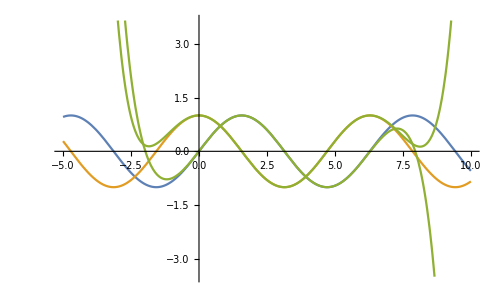

```mathematica
Func1[u_]:={Sin[u],Cos[u]};
spFuncTaylor=FindTaylor[Func1,3,10];
Plot[{Sin[u],Cos[u],("Function"/.spFuncTaylor)[u]},{u,-5,10}]
```

### JSON

```mathematica
ReplaceMemberNameWithString[object_]:=Module[{n,newobject},
n=Length[object];
newobject=Table[ToString[object[[i,1]]]-> object[[i,2]],{i,1,n}];
Return[newobject];
]
```

```mathematica
ReplaceMemberValueWithString[object_]:=Module[{n,newobject},
n=Length[object];
newobject=Table[object[[i,1]]-> TextString[object[[i,2]]],{i,1,n}];
Return[newobject];
]
```

```mathematica
ReplaceMemberValuwWithDigital[object_]:=Module[{n,newobject},
n=Length[object];
newobject=Table[object[[i,1]]-> ToExpression[object[[i,2]]],{i,1,n}];
Return[newobject];
]
```

### Array

```mathematica
Array2Dto1D[arr_]:=Module[
{nRow,nCol},
nRow=Length[arr];
nCol=Length[arr[[1]]];
Table[
arr[[
Ceiling[i1/nCol],
i1-(Ceiling[i1/nCol]-1)*nCol
]]
,{i1,1,nRow*nCol}]
];
Array1Dto2D[arr_,nCol_]:=Module[
{nRow},
nRow=Ceiling[Length[arr]/nCol];
Table[
arr[[(i1-1)*nCol+j]]
,{i1,1,nRow},{j,1,nCol}]
];
```

```mathematica
Take2D[martrix2D_,range_]:=
Table[
Take[martrix2D[[ii]],{range[[1,2]],range[[2,2]]}]
,{ii,range[[1,1]],range[[2,1]]}];
```

### Unit Convert

```mathematica
Inv[alpha_]:=Tan[alpha]-alpha;
```

```mathematica
RadToDeg[theta_]:=theta/Pi*180;
```

### Settings Operation

```mathematica
FindSettingKeyIndex[settings_,key_]:=Module[
{i},
For[i=1,i≤Length[settings],i=i+1,
If[settings[[i,1]]==key,Return[i]]
]
];
```

```mathematica
SetSettingValue[settings_,key_,value_]:=Module[
{i,newSettings},
i=FindSettingKeyIndex[settings,key];
newSettings=settings;
newSettings[[i,2]]=value;
Return[newSettings];
];
```

### GlobalVariable

#### Initialize & Clear

```mathematica
InitializeGlobalVariableIfNotExist[]:=If[ValueQ[GlobalVariable]== False,GlobalVariable={};]
```

```mathematica
ClearGlobalVariable[]:=GlobalVariable={};
```

#### Check Exsist

```mathematica
CheckGlobalVariableExsist[variableName_]:=Module[
{nameList},
InitializeGlobalVariableIfNotExist[];
nameList=Table[GlobalVariable[[i,1]],{i,1,Length[GlobalVariable]}];
MemberQ[nameList,variableName]
];
```

#### Check Index : Return 0 if variable not exist

```mathematica
CheckGlobalVariableIndex[variableName_]:=Module[
{index},
InitializeGlobalVariableIfNotExist[];
index=0;
Table[
If[GlobalVariable[[i,1]]==variableName, index=i];
,{i,1,Length[GlobalVariable]}];
index
];
```

#### Set Variable Value : Add variable if variable not exist

```mathematica
SetGlobalVariable[variableName_,value_]:=Module[
{index},
InitializeGlobalVariableIfNotExist[];
index=CheckGlobalVariableIndex[variableName];
If[index≠0,
GlobalVariable[[index,2]]=value,
GlobalVariable=Join[GlobalVariable,{variableName->value}]
];
GlobalVariable
]
```

#### Get Variable Value : Return Null if variable not exist

```mathematica
GetGlobalVariable[variableName_]:=Module[
{index},
InitializeGlobalVariableIfNotExist[];
index=CheckGlobalVariableIndex[variableName];
If[index≠0,GlobalVariable[[index,2]]]
]
```

#### Get Variable Value with default value : Return default value if variable not exist

```mathematica
GetGlobalVariableWithDefaultValue[variableName_,defualtValue_]:=Module[
{index},
InitializeGlobalVariableIfNotExist[];
index=CheckGlobalVariableIndex[variableName];
If[index≠0,GlobalVariable[[index,2]],defualtValue]
]
```

### IMG Output

```mathematica
OutputImage[filename_,img_,cmWidth_,dpi_]:=
Module[{cm,ImageWidth,outputimage},
cm=72/2.54;(*Mathematica的ImageSize單位是pt，也就是 1/72 in*)
ImageWidth=cmWidth*cm;
outputimage=Show[img,ImageSize->ImageWidth];
Export[filename,outputimage,ImageResolution->dpi];
Import[filename,ImageResolution->dpi]
]
```

## Runed

```mathematica
SetGlobalVariable[NotebookFileName[],True]
```

{C:\Data\GitHub\Power-Skiving-Mathematical-Model\Universal functions.nb→True}